```mathematica
Clear["Global`*"]
```

```mathematica
Subscript[M, o]=1.988435*^30 (*Kg*)
G = 6.67408 * 10^-11 (*m3 Kg-1 s-1*)
Subscript[Σ, MilkyWay] = 700 * Subscript[M, o] / (3.086*10^16)^2 (* Kg m-2*)
Subscript[Rd, MilkyWay]= 3200 * 3.086*10^16 (*m*)
```

1.98844×10^30

6.67408×10^-11

1.46156

9.8752×10^19

```mathematica
√(Pi*G*Subscript[Σ, MilkyWay]/Subscript[Rd, MilkyWay])
```

1.7616×10^-15

```mathematica
Vd[R_] =   √((Pi*G*Σ0/Rd)(R^2 BesselI[0,R/(2*Rd)] BesselK[0,R/(2*Rd)]-R^2 BesselI[1,R/(2*Rd)] BesselK[1,R/(2*Rd)])) 10^-3
```

1.44801×10^-8 √((Σ0 (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)]))/Rd)

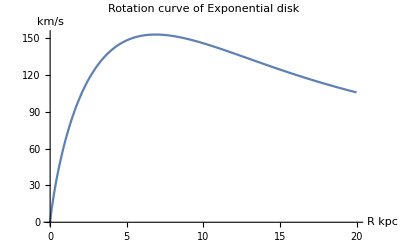

```mathematica
Plot[Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, MilkyWay],Rd-> Subscript[Rd, MilkyWay]} ,{R,0,20},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of Exponential disk],LabelStyle->{GrayLevel[0]},PlotRange->All]
```

Rotational velocity of a Spherical distribution having the same mass as the exponential disk at every R.

```mathematica
Vs[R_] = √(2*N[Pi]*Subscript[Σ, MilkyWay]*G*(Rd*Rd/(R*3.086*10^19))*(1-Exp[-(R*3.086*10^19)/Rd]*(1+(R*3.086*10^19)/Rd)))*10^-3/.Rd->Subscript[Rd, MilkyWay]
```

440.091 √((1-ⅇ^(-0.3125 R) (1+0.3125 R))/R)

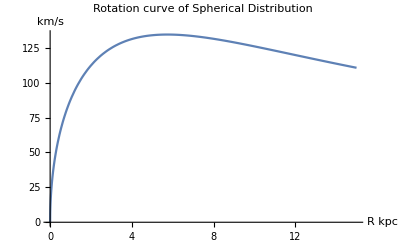

```mathematica
Plot[Vs[R],{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of Spherical Distribution],LabelStyle->{GrayLevel[0]},PlotRange->All]
```

```mathematica
Vpoint[R_] =√(2*Pi*G*Subscript[Σ, MilkyWay]*Rd*Rd/(R*3.086*10^19))*10^-3/.Rd->Subscript[Rd, MilkyWay]
```

440.091 √(1/R)

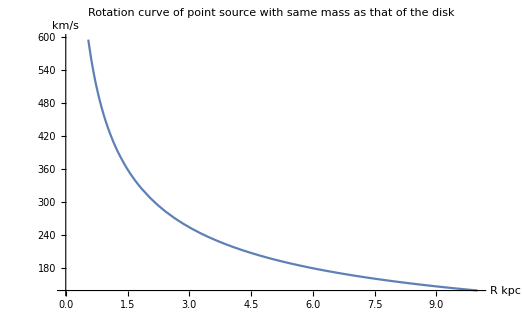

```mathematica
Plot[Vpoint[R],{R,0,10},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of point source with same mass as that of the disk ],LabelStyle->{GrayLevel[0]}]
```

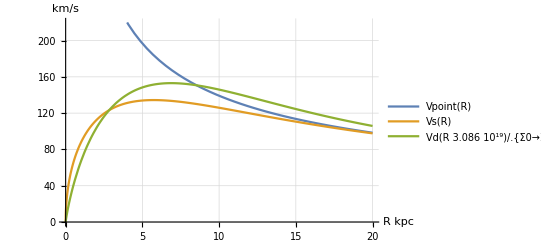

```mathematica
Plot[{Vpoint[R],Vs[R],Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, MilkyWay],Rd-> Subscript[Rd, MilkyWay]}},{R,0,20},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLegends->"Expressions",GridLines-> Automatic]
```

Isothermal profiles:
1.Milky way

```mathematica
ρMilkyway = 0.035* Subscript[M, o] / (3.086*10^16)^3 (* Kg m-3*)
```

2.36805×10^-21

```mathematica
RcMilkyway = 5000* 3.086*10^16 (*m*)
```

1.543×10^20

```mathematica
ρ[R_] = ρ0/(1+(R)^2/Rc^2)
```

ρ0/(1+R^2/Rc^2)

```mathematica
Subscript[ϕ, halo][R_,z_] = (4*Pi*G*ρ0*Rc^2)(0.5*Log[Rc^2+R^2+z^2]+Rc/(√(R^2+z^2))*ArcTan[(√(R^2+z^2))/Rc ]-1)
```

8.3869×10^-10 Rc^2 ρ0 (-1+(Rc ArcTan[(√(R^2+z^2))/Rc])/(√(R^2+z^2))+0.5 Log[R^2+Rc^2+z^2])

```mathematica
Vhalo[R_] = √(R*D[Subscript[ϕ, halo][R,z]/.z->0,R])*10^-3
```

2.89601×10^-8 √(R Rc^2 ρ0 (1/(R (1+R^2/Rc^2))+(1. R)/(R^2+Rc^2)-(R Rc ArcTan[(√(R^2))/Rc])/((R^2)^(3/2))))

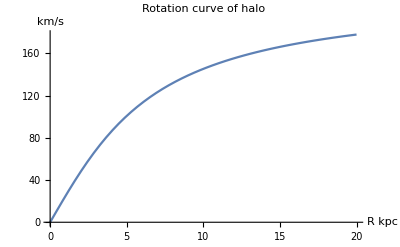

```mathematica
Plot[Vhalo[R*3.086*10^19]/.{ρ0->ρMilkyway,Rc->RcMilkyway},{R,0,20},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of halo],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Vnet[R_] = √(Vhalo[R]^2 + Vd[R]^2)
```

√(8.3869×10^-16 R Rc^2 ρ0 (1/(R (1+R^2/Rc^2))+(1. R)/(R^2+Rc^2)-(R Rc ArcTan[(√(R^2))/Rc])/((R^2)^(3/2)))+(2.09672×10^-16 Σ0 (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)]))/Rd)

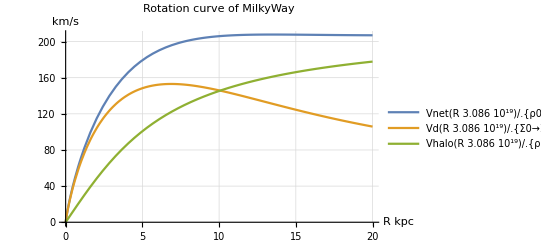

```mathematica
Plot[{Vnet[R*3.086*10^19]/.{ρ0->ρMilkyway,Rc->RcMilkyway,Σ0->Subscript[Σ, MilkyWay],Rd-> Subscript[Rd, MilkyWay]},Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, MilkyWay],Rd-> Subscript[Rd, MilkyWay]},Vhalo[R*3.086*10^19]/.{ρ0->ρMilkyway,Rc->RcMilkyway}},{R,0,20},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of MilkyWay],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions",GridLines->Automatic]
```

### UGC7321

```mathematica
ρUGC7321= 0.057* Subscript[M, o] / (3.086*10^16)^3 (* Kg m-3*)
RcUGC7321 = 2500* 3.086*10^16 (*m*)
```

3.85655×10^-21

7.715×10^19

```mathematica
Subscript[Σ, UGC7321] = 50.2 * Subscript[M, o] / (3.086*10^16)^2 (* Kg m-2*)
Subscript[Rd, UGC7321]= 2100* 3.086*10^16  (*m*)
```

0.104815

6.4806×10^19

```mathematica
Vnet[R]
```

√(8.3869×10^-16 R Rc^2 ρ0 (1/(R (1+R^2/Rc^2))+(1. R)/(R^2+Rc^2)-(R Rc ArcTan[(√(R^2))/Rc])/((R^2)^(3/2)))+(2.09672×10^-16 Σ0 (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)]))/Rd)

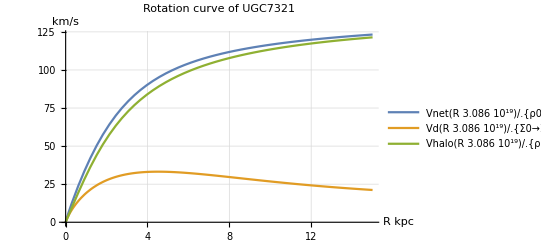

```mathematica
Plot[{Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},Vhalo[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions",GridLines->Automatic,FrameTicks->LinTicks[0,6]]
```

```mathematica
SetOptions[LinTicks,MajorTickLength->{0.02,0},MinorTickLength->{0.013,0}];
```

SetOptions::optnf: MajorTickLength is not a known option for LinTicks.

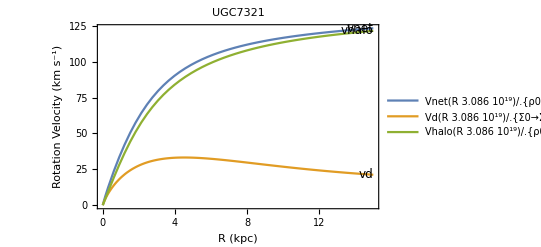

```mathematica
Plot[{Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},Vhalo[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321}},{R,0,15},Frame-> True,FrameLabel->{HoldForm["R (kpc)"],HoldForm["Rotation Velocity " "(km s^-1)"]},LabelStyle->Directive[Black,FontSize->12],PlotLabel->HoldForm[UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions",PlotLabels->Placed[{"vnet","vd","vhalo"},{Scaled[1],Before}]]
```

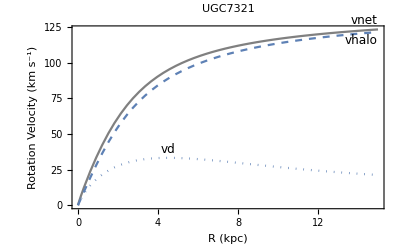

```mathematica
Show[Plot[Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},{R,0,15},Frame-> True,FrameLabel->{HoldForm["R (kpc)"],HoldForm["Rotation Velocity " "(km s^-1)"]},LabelStyle->Directive[Black,FontSize->12],PlotLabel->HoldForm[UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions",PlotLabels->Placed["vnet",Above],PlotStyle->Gray],
Plot[Vhalo[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321},{R,0,15},Frame-> True,FrameLabel->{HoldForm["R (kpc)"],HoldForm["Rotation Velocity " "(km s^-1)"]},LabelStyle->Directive[Black,FontSize->12],PlotLabel->HoldForm[UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions",PlotLabels->Placed["vhalo",{Scaled[1.,80],Below}],PlotStyle->Dashed],
Plot[Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},{R,0,15},Frame-> True,FrameLabel->{HoldForm["R (kpc)"],HoldForm["Rotation Velocity " "(km s^-1)"]},LabelStyle->Directive[Black,FontSize->12],PlotLabel->HoldForm[UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions",PlotLabels->Placed[{"vd"},Above],PlotStyle->Dotted]]
```

```mathematica
Plot[{Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},Vhalo[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions",GridLines->Automatic]
```

-Graphics-

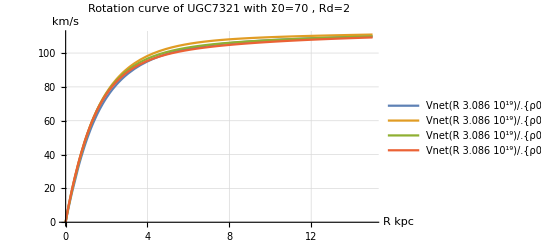

```mathematica
Plot[{Vnet[R*3.086*10^19]/.{ρ0->(0.126/0.057)*ρUGC7321,Rc->(1.4/2.5)*RcUGC7321,Σ0->(70/50.2)*Subscript[Σ, UGC7321],Rd->(2/2.1)* Subscript[Rd, UGC7321]},Vnet[R*3.086*10^19]/.{ρ0->(0.126/0.057)*ρUGC7321,Rc->(1.4/2.5)*RcUGC7321,Σ0->(100/50.2)*Subscript[Σ, UGC7321],Rd->(2/2.1)* Subscript[Rd, UGC7321]},Vnet[R*3.086*10^19]/.{ρ0->(0.126/0.057)*ρUGC7321,Rc->(1.4/2.5)*RcUGC7321,Σ0->(100/50.2)*Subscript[Σ, UGC7321],Rd->(1.7/2.1)* Subscript[Rd, UGC7321]},Vnet[R*3.086*10^19]/.{ρ0->(0.126/0.057)*ρUGC7321,Rc->(1.4/2.5)*RcUGC7321,Σ0->(100/50.2)*Subscript[Σ, UGC7321],Rd->(1.5/2.1)* Subscript[Rd, UGC7321]}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of UGC7321 with Σ0 = 70 "," Rd = 2 ],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions",GridLines->Automatic,PlotRange->All]
```

```mathematica
Vd[R]
```

1.44801×10^-8 √((Σ0 (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)]))/Rd)

```mathematica
(*Manipulate[Plot[{Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->0.10481495991555954,Rd-> Subscript[Rd, UGC7321]},Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Σ*(Subscript[M, o] / (3.086*10^16)^2),Rd-> Rdr*(3.086*10^19)},Vd[R*3.086*10^19]/.{Σ0->Σ*(Subscript[M, o] / (3.086*10^16)^2),Rd-> Rdr*(3.086*10^19)},Vhalo[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321},Vhalo[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions"],{Σ,0,100,Appearance->"Labeled"},{Rdr,1,2.5,Appearance->"Labeled"}]*)
```

```mathematica
Vnettest = Table[Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},{R,0.5,8,0.1}];
```

```mathematica
Length[Vnettest]
```

76

Test varying both Σ0 and Rd

```mathematica
Vnettest = Table[Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},{R,0.5,8,0.1}];
```

```mathematica
Vnettest3 = Table[Transpose[Table[Table[Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->a,Rd-> b},{a,0,4*Subscript[Σ, UGC7321],0.01}],{R,0.5,8,0.1}]],{b, 4* 10^19,9* 10^19,0.1*10^19}];
```

```mathematica
Subscript[Σ, UGC7321]
```

0.104815

```mathematica
Dimensions[Vnettest3]
```

{51,42,76}

```mathematica
(*Vnettest3new = Table[Transpose[Table[Table[Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->a,Rd-> b},{a,0,4*Subscript[Σ, UGC7321],0.01}],{R,0.5,5.5,0.01}]],{b, 6* 10^19,9* 10^19,0.1*10^19}];*)
```

#### Kolmogorov-Smirnov test

```mathematica
k3n = Table[Table[KolmogorovSmirnovTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95],{n,1,42}],{m,1,31}];
```

```mathematica
k3 = Table[Table[KolmogorovSmirnovTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95],{n,1,42}],{m,1,31}];
```

```mathematica
k32pc = Table[Table[KolmogorovSmirnovTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.98],{n,1,42}],{m,1,31}];
```

```mathematica
k31pc = Table[Table[KolmogorovSmirnovTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.99],{n,1,42}],{m,1,31}];
```

```mathematica
(*k3pn = Table[Table[KolmogorovSmirnovTest[Vnettest,Vnettest3new[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95]["PValue"],{n,1,42}],{m,1,31}];*)
```

```mathematica
k3[[1]][[1]]["PValue"]
```

0.301162

```mathematica
(*k3p = Table[Table[KolmogorovSmirnovTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95]["PValue"],{n,1,42}],{m,1,31}];*)
```

```mathematica
(*k3p2pc = Table[Table[KolmogorovSmirnovTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.98]["PValue"],{n,1,42}],{m,1,31}];*)
```

```mathematica
(*k3p1pc = Table[Table[KolmogorovSmirnovTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.99]["PValue"],{n,1,42}],{m,1,31}];*)
```

```mathematica
k32pc[[1]][[1]]["ShortTestConclusion"]
```

Reject

```mathematica
k31pc[[1]][[1]]["TestConclusion"]
```

The null hypothesis that the datasets have the same distribution is rejected at the 99. percent level based on the Kolmogorov-Smirnov test.

```mathematica
Dimensions[%170]
```

{1}

```mathematica
k3conclusionsn = Table[Table[k3n[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,31}];
```

$Aborted

```mathematica
k3conclusions = Table[Table[k3[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,31}];
```

```mathematica
k3conclusions2pc = Table[Table[k32pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,31}];
```

```mathematica
k3conclusions1pc = Table[Table[k31pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,31}];
```

```mathematica
Length[verticle]
```

31

```mathematica
k3newn = k3conclusionsn/.{"Do not reject" -> ColorData["BrassTones"],"Reject"-> 0};
```

```mathematica
k3new = k3conclusions/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
k3new2pc = k3conclusions2pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
k3new1pc = k3conclusions1pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
TableForm[k3new,TableHeadings->{verticle, horizontal},TableSpacing->{2, 1}]
```

| 0. | 4.78939 | 9.57879 | 14.3682 | 19.1576 | 23.947 | 28.7364 | 33.5257 | 38.3151 | 43.1045 | 47.8939 | 52.6833 | 57.4727 | 62.2621 | 67.0515 | 71.8409 | 76.6303 | 81.4197 | 86.2091 | 90.9985 | 95.7879 | 100.577 | 105.367 | 110.156 | 114.945 | 119.735 | 124.524 | 129.314 | 134.103 | 138.892 | 143.682 | 148.471 | 153.261 | 158.05 | 162.839 | 167.629 | 172.418 | 177.208 | 181.997 | 186.786 | 191.576 | 196.365
1.29618 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.32858 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.36099 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.39339 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.42579 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.4582 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.4906 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.52301 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.55541 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.58782 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.62022 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.65262 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.68503 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.71743 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.74984 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.78224 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.81465 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.84705 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.87946 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.91186 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.94426 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.97667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.00907 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.04148 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.07388 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.10629 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.13869 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.1711 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.2035 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.2359 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.26831 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Show[%244,FrameLabel->{{HoldForm[Rd],None},{HoldForm[Surface Density],None}},PlotLabel->HoldForm[KS Test],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%244,FrameLabel→{{Rd,None},{Surface Density,None}},PlotLabel→KS Test,LabelStyle→{GrayLevel[0]}]

```mathematica
Show[%247,Background->White]
```

Show::gtype: Out is not a type of graphics.

Show[%247,Background→GrayLevel[1]]

```mathematica
Dimensions[k3new]
```

{31,42}

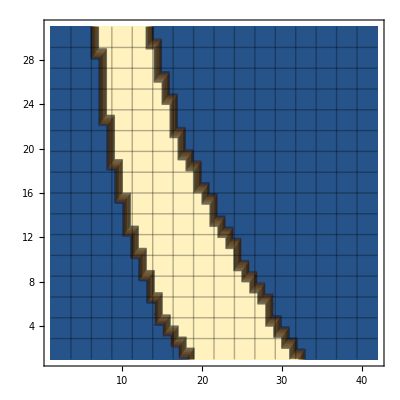

```mathematica
ListContourPlot[k3new1pc,Mesh->Automatic,MeshFunctions->Automatic]
```

```mathematica
ok = Table[Table[{verticle[[m]],horizontal[[n]],k3new[[m]][[n]]},{m,1,31}],{n,1,42}];
```

```mathematica
Export["ok.dat",Flatten[ok]]
```

ok.dat

```mathematica
Flatten[ok];
```

```mathematica
Dimensions[ok]
```

{42,31,3}

```mathematica
Times@@{42,31,3}
```

3906

```mathematica
Transpose[ok];
```

```mathematica
MatrixPlot[ok];
```

MatrixPlot::mat0: Argument {{{1.29618,0.,0},{1.32858,0.,0},{1.36099,0.,0},{1.39339,0.,0},{1.42579,0.,0},{1.4582,0.,0},{1.4906,0.,0},{1.52301,0.,0},{1.55541,0.,0},{1.58782,0.,0},«12»,{2.00907,0.,0},{2.04148,0.,0},{2.07388,0.,0},{2.10629,0.,0},{2.13869,0.,0},{2.1711,0.,0},{2.2035,0.,0},{2.2359,0.,0},{2.26831,0.,0}},«40»,{{«1»},«30»}} at position 1 is not a matrix.

```mathematica
ok//MatrixForm
```

(1)
 |  |  |  |

```mathematica
Dimensions[%141]
```

{1}

```mathematica
ListPointPlot3D[Transpose[ok]]
```

-Graphics3D-

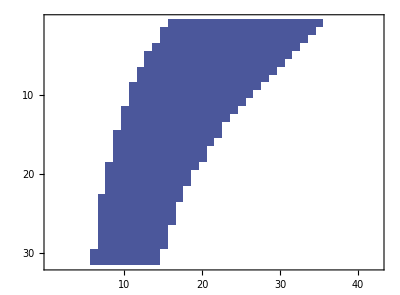
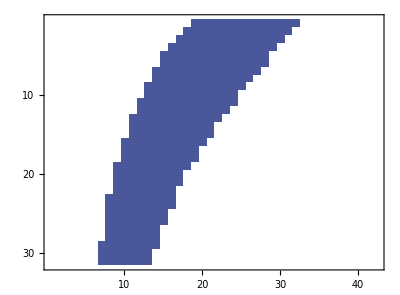
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MatrixPlot[a,PlotTheme->"Scientific"],{a,{k3new,k3new2pc,k3new1pc}}]
```

```mathematica
Show[%209,PlotLabel->HoldForm[pc KS test-1 %],LabelStyle->{FontFamily->"Noto Sans Mono CJK TC",GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%209,PlotLabel→pc KS test-1 %,LabelStyle→{FontFamily→Noto Sans Mono CJK TC,GrayLevel[0]}]

```mathematica
Dimensions[k3new]
```

{31,42}

```mathematica
Sum[Tally[k3new[[n]]],{n,31}]
```

{{0,881},{31,421}}

```mathematica
Sum[Tally[k3new2pc[[n]]],{n,31}]
```

{{0,970},{31,332}}

```mathematica
Sum[Tally[k3new1pc[[n]]],{n,31}]
```

{{0,970},{31,332}}

```mathematica
(*For[m=1,m<31,m++,For[n=1,n<42,n++,If[k3conclusionsn[[m]][[n]]== "Do not reject" ,k3newn[[m]][[n]] = k3pn[[m]][[n]],k3newn[[m]][[n]] =0]] ]*)
```

```mathematica
For[m=1,m<31,m++,For[n=1,n<42,n++,If[k3conclusions[[m]][[n]]== "Do not reject" ,k3new[[m]][[n]] = k3[[m]][[n]]["PValue"],k3new[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<31,m++,For[n=1,n<42,n++,If[k3conclusions2pc[[m]][[n]]== "Do not reject" ,k3new2pc[[m]][[n]] = k32pc[[m]][[n]]["PValue"],k3new2pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<31,m++,For[n=1,n<42,n++,If[k3conclusions1pc[[m]][[n]]== "Do not reject" ,k3new1pc[[m]][[n]] = k31pc[[m]][[n]]["PValue"],k3new1pc[[m]][[n]] =0]] ]
```

#### Chi Squared test

```mathematica
Ck3n = Table[Table[PearsonChiSquareTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95],{n,1,42}],{m,1,31}];
```

```mathematica
Ck3 = Table[Table[PearsonChiSquareTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95],{n,1,42}],{m,1,31}];
```

```mathematica
Ck32pc = Table[Table[PearsonChiSquareTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.98],{n,1,42}],{m,1,31}];
```

```mathematica
Ck31pc = Table[Table[PearsonChiSquareTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.99],{n,1,42}],{m,1,31}];
```

```mathematica
(*Ck3pn = Table[Table[PearsonChiSquareTest[Vnettest,Vnettest3new[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95]["PValue"],{n,1,42}],{m,1,31}];*)
```

```mathematica
Ck3p = Table[Table[PearsonChiSquareTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95]["PValue"],{n,1,42}],{m,1,31}];
```

```mathematica
Ck3p2pc = Table[Table[PearsonChiSquareTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.98]["PValue"],{n,1,42}],{m,1,31}];
```

```mathematica
Ck3p1pc = Table[Table[PearsonChiSquareTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.99]["PValue"],{n,1,42}],{m,1,31}];
```

```mathematica
Ck3conclusionsn = Table[Table[Ck3n[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,31}];
```

```mathematica
Ck3conclusions = Table[Table[Ck3[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,31}];
```

```mathematica
Ck3conclusions2pc = Table[Table[Ck32pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,31}];
```

```mathematica
Ck3conclusions1pc = Table[Table[Ck31pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,31}];
```

```mathematica
Ck3newn = Ck3conclusionsn/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
Ck3new = Ck3conclusions/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
Ck3new2pc = Ck3conclusions2pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
Ck3new1pc = Ck3conclusions1pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
TableForm[Ck3new,TableHeadings->{verticle, horizontal},TableSpacing->{2, 1}];
```

```mathematica
For[m=1,m<31,m++,For[n=1,n<42,n++,If[Ck3conclusionsn[[m]][[n]]== "Do not reject" ,Ck3newn[[m]][[n]] = Ck3pn[[m]][[n]],Ck3newn[[m]][[n]] =0]] ]
```

Part::partd: Part specification Ck3pn⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of Ck3pn⟦1⟧ does not exist.

Part::partw: Part 4 of Ck3pn⟦1⟧ does not exist.

Part::partw: Part 5 of Ck3pn⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
For[m=1,m<31,m++,For[n=1,n<42,n++,If[Ck3conclusions[[m]][[n]]== "Do not reject" ,Ck3new[[m]][[n]] = Ck3p[[m]][[n]],Ck3new[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<31,m++,For[n=1,n<42,n++,If[Ck3conclusions2pc[[m]][[n]]== "Do not reject" ,Ck3new2pc[[m]][[n]] = Ck3p2pc[[m]][[n]],Ck3new2pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<31,m++,For[n=1,n<42,n++,If[Ck3conclusions1pc[[m]][[n]]== "Do not reject" ,Ck3new1pc[[m]][[n]] = Ck3p1pc[[m]][[n]],Ck3new1pc[[m]][[n]] =0]] ]
```

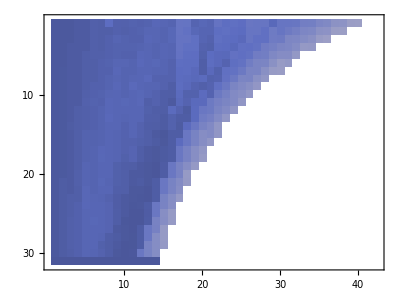
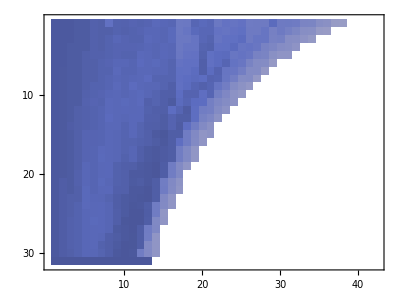
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MatrixPlot[a,PlotTheme->"Scientific"],{a,{Ck3new,Ck3new2pc,Ck3new1pc}}]
```

```mathematica
TableForm[Ck3new,TableHeadings->{verticle, horizontal},TableSpacing->{2, 1}];
```

```mathematica
%124
```

%124

#### Σ0→2*Σ_UGC7321

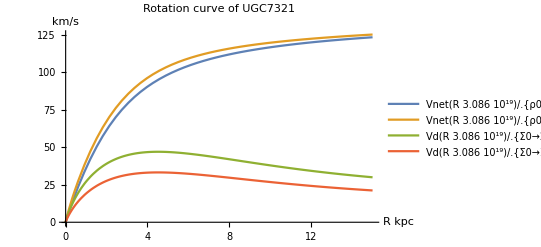

```mathematica
Plot[{Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->2*Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},Vd[R*3.086*10^19]/.{Σ0->2*Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions"]
```

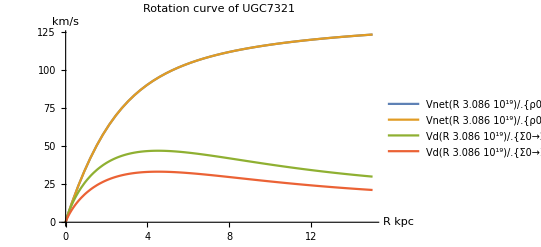

```mathematica
Plot[{Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},Vd[R*3.086*10^19]/.{Σ0->2*Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions"]
```

```mathematica
(*Manipulate[Plot[{Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->0.10481495991555954,Rd-> Subscript[Rd, UGC7321]},Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Σ*(Subscript[M, o] / (3.086*10^16)^2),Rd-> Rdr*(3.086*10^19)},Vd[R*3.086*10^19]/.{Σ0->Σ*(Subscript[M, o] / (3.086*10^16)^2),Rd-> Rdr*(3.086*10^19)}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions"],{Σ,0,200,Appearance->"Labeled"},{Rdr,1,2.5,Appearance->"Labeled"}]*)
```

#### Varying the halo parameters

```mathematica
hVnettest3 = Table[Transpose[Table[Table[Vnet[R*3.086*10^19]/.{ρ0->2*ρUGC7321,Rc->RcUGC7321,Σ0->a,Rd-> b},{a,0,4*Subscript[Σ, UGC7321],0.01}],{R,0.5,8,0.1}]],{b, 4* 10^19,9* 10^19,0.1*10^19}];
```

```mathematica
hVnettest = Table[Vnet[R*3.086*10^19]/.{ρ0->2*ρUGC7321,Rc->RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},{R,0.5,8,0.1}];
```

```mathematica
ρUGC7321
```

3.85655×10^-21

#### Kolmogorov-Smirnov test

```mathematica
hk3n = Table[Table[KolmogorovSmirnovTest[hVnettest,hVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95],{n,1,42}],{m,1,31}];
```

```mathematica
hk3 = Table[Table[KolmogorovSmirnovTest[hVnettest,hVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95],{n,1,42}],{m,1,31}];
```

```mathematica
hk32pc = Table[Table[KolmogorovSmirnovTest[hVnettest,hVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.98],{n,1,42}],{m,1,31}];
```

```mathematica
hk31pc = Table[Table[KolmogorovSmirnovTest[hVnettest,hVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.99],{n,1,42}],{m,1,31}];
```

```mathematica
(*k3pn = Table[Table[KolmogorovSmirnovTest[Vnettest,Vnettest3new[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95]["PValue"],{n,1,42}],{m,1,31}];*)
```

```mathematica
hk3[[1]][[1]]["PValue"]
```

0.973452

```mathematica
(*k3p = Table[Table[KolmogorovSmirnovTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95]["PValue"],{n,1,42}],{m,1,31}];*)
```

```mathematica
(*k3p2pc = Table[Table[KolmogorovSmirnovTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.98]["PValue"],{n,1,42}],{m,1,31}];*)
```

```mathematica
(*k3p1pc = Table[Table[KolmogorovSmirnovTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.99]["PValue"],{n,1,42}],{m,1,31}];*)
```

```mathematica
k32pc[[1]][[1]]["ShortTestConclusion"]
```

Reject

```mathematica
k31pc[[1]][[1]]["TestConclusion"]
```

The null hypothesis that the datasets have the same distribution is rejected at the 99. percent level based on the Kolmogorov-Smirnov test.

```mathematica
Dimensions[%170]
```

{1}

```mathematica
hk3conclusionsn = Table[Table[hk3n[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,31}];
```

```mathematica
hk3conclusions = Table[Table[hk3[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,31}];
```

$Aborted

```mathematica
hk3conclusions2pc = Table[Table[hk32pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,31}];
```

```mathematica
hk3conclusions1pc = Table[Table[hk31pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,31}];
```

```mathematica
horizontal = Table[j,{j,0,4*Subscript[Σ, UGC7321],0.01}]/(Subscript[M, o] / (3.086*10^16)^2 )
```

{0.,4.78939,9.57879,14.3682,19.1576,23.947,28.7364,33.5257,38.3151,43.1045,47.8939,52.6833,57.4727,62.2621,67.0515,71.8409,76.6303,81.4197,86.2091,90.9985,95.7879,100.577,105.367,110.156,114.945,119.735,124.524,129.314,134.103,138.892,143.682,148.471,153.261,158.05,162.839,167.629,172.418,177.208,181.997,186.786,191.576,196.365}

```mathematica
Length[horizontal]
```

42

```mathematica
verticle = Table[i,{i, 4* 10^19,7* 10^19,0.1*10^19}]/ (3.086*10^19)
```

{1.29618,1.32858,1.36099,1.39339,1.42579,1.4582,1.4906,1.52301,1.55541,1.58782,1.62022,1.65262,1.68503,1.71743,1.74984,1.78224,1.81465,1.84705,1.87946,1.91186,1.94426,1.97667,2.00907,2.04148,2.07388,2.10629,2.13869,2.1711,2.2035,2.2359,2.26831}

```mathematica
Length[verticle]
```

31

```mathematica
hk3newn = hk3conclusionsn/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
hk3new = hk3conclusions/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
hk3new2pc = hk3conclusions2pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
hk3new1pc = hk3conclusions1pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
TableForm[k3new,TableHeadings->{verticle, horizontal},TableSpacing->{2, 1}]
```

| 0. | 4.78939 | 9.57879 | 14.3682 | 19.1576 | 23.947 | 28.7364 | 33.5257 | 38.3151 | 43.1045 | 47.8939 | 52.6833 | 57.4727 | 62.2621 | 67.0515 | 71.8409 | 76.6303 | 81.4197 | 86.2091 | 90.9985 | 95.7879 | 100.577 | 105.367 | 110.156 | 114.945 | 119.735 | 124.524 | 129.314 | 134.103 | 138.892 | 143.682 | 148.471 | 153.261 | 158.05 | 162.839 | 167.629 | 172.418 | 177.208 | 181.997 | 186.786 | 191.576 | 196.365
1.29618 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.973452 | 0.973452 | 0.996986 | 0.996986 | 0.999954 | 0.999954 | 1. | 1. | 1. | 0.999954 | 0.999954 | 0.999954 | 0.999954 | 0.996986 | 0.996986 | 0.996986 | 0.973452 | 0.973452 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.32858 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.973452 | 0.973452 | 0.996986 | 0.996986 | 0.999954 | 0.999954 | 1. | 1. | 1. | 1. | 0.999954 | 0.999954 | 0.999954 | 0.996986 | 0.996986 | 0.996986 | 0.973452 | 0.973452 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.36099 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.973452 | 0.996986 | 0.996986 | 0.999954 | 0.999954 | 1. | 1. | 1. | 1. | 0.999954 | 0.999954 | 0.999954 | 0.999954 | 0.996986 | 0.996986 | 0.973452 | 0.973452 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.39339 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.973452 | 0.996986 | 0.996986 | 0.999954 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.999954 | 0.999954 | 0.996986 | 0.996986 | 0.973452 | 0.973452 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.42579 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.973452 | 0.996986 | 0.996986 | 0.999954 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.999954 | 0.999954 | 0.996986 | 0.996986 | 0.973452 | 0.973452 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.4582 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.973452 | 0.996986 | 0.999954 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.999954 | 0.996986 | 0.996986 | 0.996986 | 0.973452 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.4906 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.973452 | 0.996986 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.999954 | 0.999954 | 0.996986 | 0.996986 | 0.973452 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.52301 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.973452 | 0.996986 | 0.999954 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.999954 | 0.996986 | 0.996986 | 0.973452 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.55541 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.973452 | 0.996986 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.999954 | 0.996986 | 0.996986 | 0.973452 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.58782 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.999954 | 0.996986 | 0.973452 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.62022 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.999954 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.999954 | 0.996986 | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.65262 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.996986 | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.68503 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.999954 | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.71743 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.74984 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.996986 | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.78224 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.999954 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.81465 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.84705 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.87946 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.91186 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.94426 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.97667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.00907 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.04148 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.996986 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.07388 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.10629 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 0.999954 | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.13869 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 1. | 1. | 1. | 1. | 1. | 0.999954 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.1711 | 0 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.999954 | 1. | 1. | 1. | 1. | 1. | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.2035 | 0 | 0 | 0 | 0 | 0 | 0 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 0.999954 | 0.996986 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.2359 | 0 | 0 | 0 | 0 | 0 | 0.973452 | 0.996986 | 0.999954 | 1. | 1. | 1. | 1. | 0.999954 | 0.973452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.26831 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Show[%244,FrameLabel->{{HoldForm[Rd],None},{HoldForm[Surface Density],None}},PlotLabel->HoldForm[KS Test],LabelStyle->{GrayLevel[0]}]
```

Show[%244,FrameLabel→{{Rd,None},{Surface Density,None}},PlotLabel→KS Test,LabelStyle→{GrayLevel[0]}]

```mathematica
Show[%247,Background->White]
```

Show[%247,Background→GrayLevel[1]]

```mathematica
Dimensions[k3new]
```

{31,42}

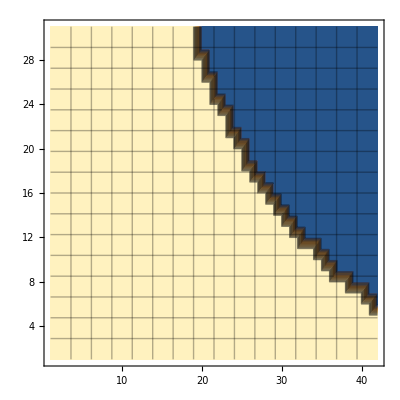

```mathematica
ListContourPlot[hk3new,Mesh->Automatic,MeshFunctions->Automatic]
```

```mathematica
ok//MatrixForm
```

(1)
 |  |  |  |

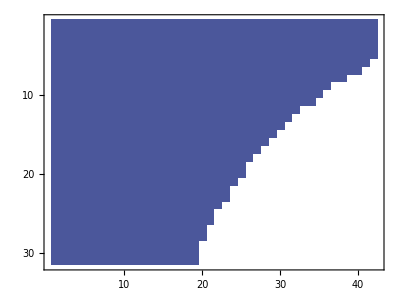
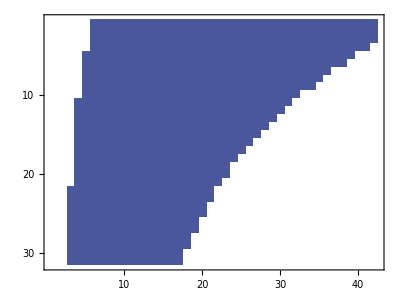
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MatrixPlot[a,PlotTheme->"Scientific"],{a,{hk3new,hk3new2pc,hk3new1pc}}]
```

```mathematica
(*For[m=1,m<31,m++,For[n=1,n<42,n++,If[k3conclusionsn[[m]][[n]]== "Do not reject" ,k3newn[[m]][[n]] = k3pn[[m]][[n]],k3newn[[m]][[n]] =0]] ]*)
```

```mathematica
For[m=1,m<31,m++,For[n=1,n<42,n++,If[hk3conclusions[[m]][[n]]== "Do not reject" ,hk3new[[m]][[n]] = hk3[[m]][[n]]["PValue"],hk3new[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<31,m++,For[n=1,n<42,n++,If[hk3conclusions2pc[[m]][[n]]== "Do not reject" ,hk3new2pc[[m]][[n]] = hk32pc[[m]][[n]]["PValue"],hk3new2pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<31,m++,For[n=1,n<42,n++,If[hk3conclusions1pc[[m]][[n]]== "Do not reject" ,hk3new1pc[[m]][[n]] = hk31pc[[m]][[n]]["PValue"],hk3new1pc[[m]][[n]] =0]] ]
```

```mathematica
Vnet[3]
```

√(2.51607×10^-15 Rc^2 ρ0 (1/(3 (1+9/Rc^2))+3./(9+Rc^2)-1/9 Rc ArcTan[3/Rc])+(2.09672×10^-16 Σ0 (9 BesselI[0,3/(2 Rd)] BesselK[0,3/(2 Rd)]-9 BesselI[1,3/(2 Rd)] BesselK[1,3/(2 Rd)]))/Rd)

#### Okdata analysis - Varying disk parameters

```mathematica
Rdata = {0,0.436332,0.872665,1.309,1.74533,2.18166,2.61799,3.05433,3.49066,3.92699,4.36332,4.79966,5.23599,5.67232,6.10865,6.54499,6.98132,7.41765,7.85398,8.29032,8.72665,9.16298,9.59931,10.0356,10.472,10.9083,11.3446,11.781,12.2173}
```

{0,0.436332,0.872665,1.309,1.74533,2.18166,2.61799,3.05433,3.49066,3.92699,4.36332,4.79966,5.23599,5.67232,6.10865,6.54499,6.98132,7.41765,7.85398,8.29032,8.72665,9.16298,9.59931,10.0356,10.472,10.9083,11.3446,11.781,12.2173}

```mathematica
okVnettest3 = Table[Transpose[Table[Table[Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->a,Rd-> b},{a,0,4*Subscript[Σ, UGC7321],0.01}],{R,Drop[Rdata,1]}]],{b, 4* 10^19,9* 10^19,0.1*10^19}]
```

{{1},49,{{13.8558,27.0057,38.9452,49.4462,58.506,66.2509,72.8574,78.5049,83.3553,87.5461,91.1904,94.3802,4,105.683,107.305,108.779,110.124,111.356,112.488,113.531,114.497,115.391,116.224,116.999,117.724},40,{1}}}
 |  |  |  |

```mathematica
Dimensions[%208]
```

{1}

```mathematica
okoksodata = {{0.436332,24.85},{0.872665,39.599999999999994},{1.309,52.65},{1.74533,63.5},{2.18166,72.25},{2.61799,84.69999999999999},{3.05433,84.1},{3.49066,91.25},{3.92699,91.44999999999999},{4.36332,92.95},{4.79966,94.75},{5.23599,96.55000000000001},{5.67232,100.6},{6.10865,99.85},{6.54499,102.44999999999999},{6.98132,101.80000000000001},{7.41765,102.45},{7.85398,103.75},{8.29032,106.45},{8.72665,106.6},{9.16298,104.85},{9.59931,104.25},{10.0356,105.3},{10.472,103.25},{10.9083,103.30000000000001},{11.3446,102.94999999999999},{11.781,104.75},{12.2173,98.75}}
```

{{0.436332,24.85},{0.872665,39.6},{1.309,52.65},{1.74533,63.5},{2.18166,72.25},{2.61799,84.7},{3.05433,84.1},{3.49066,91.25},{3.92699,91.45},{4.36332,92.95},{4.79966,94.75},{5.23599,96.55},{5.67232,100.6},{6.10865,99.85},{6.54499,102.45},{6.98132,101.8},{7.41765,102.45},{7.85398,103.75},{8.29032,106.45},{8.72665,106.6},{9.16298,104.85},{9.59931,104.25},{10.0356,105.3},{10.472,103.25},{10.9083,103.3},{11.3446,102.95},{11.781,104.75},{12.2173,98.75}}

```mathematica
oksodata= Flatten[Drop[okoksodata,None,{1}]]
```

{24.85,39.6,52.65,63.5,72.25,84.7,84.1,91.25,91.45,92.95,94.75,96.55,100.6,99.85,102.45,101.8,102.45,103.75,106.45,106.6,104.85,104.25,105.3,103.25,103.3,102.95,104.75,98.75}

```mathematica
newokVnettest3[[1]][[1]]
```

newokVnettest3

```mathematica
okk35pc = Table[Table[PearsonChiSquareTest[RotdataUGC7321,newokVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.52],{n,1,42}],{m,1,51}];
```

$Aborted

```mathematica
okk32pc = Table[Table[PearsonChiSquareTest[RotdataUGC7321,newokVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.53],{n,1,42}],{m,1,51}];
```

Part::partd: Part specification newokVnettest3⟦1⟧ is longer than depth of object.

PearsonChiSquareTest::rctnln: The argument RotdataUGC7321 at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array.

Part::partd: Part specification newokVnettest3⟦1⟧ is longer than depth of object.

PearsonChiSquareTest::rctnln: The argument RotdataUGC7321 at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array.

Part::partd: Part specification newokVnettest3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of newokVnettest3⟦1⟧ does not exist.

PearsonChiSquareTest::rctnln: The argument RotdataUGC7321 at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array.

General::stop: Further output of PearsonChiSquareTest::rctnln will be suppressed during this calculation.

Part::partw: Part 4 of newokVnettest3⟦1⟧ does not exist.

Part::partw: Part 5 of newokVnettest3⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
okk31pc = Table[Table[PearsonChiSquareTest[RotdataUGC7321,newokVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.54],{n,1,42}],{m,1,51}];
```

Part::partd: Part specification newokVnettest3⟦1⟧ is longer than depth of object.

PearsonChiSquareTest::rctnln: The argument RotdataUGC7321 at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array.

Part::partd: Part specification newokVnettest3⟦1⟧ is longer than depth of object.

PearsonChiSquareTest::rctnln: The argument RotdataUGC7321 at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array.

Part::partd: Part specification newokVnettest3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of newokVnettest3⟦1⟧ does not exist.

PearsonChiSquareTest::rctnln: The argument RotdataUGC7321 at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array.

General::stop: Further output of PearsonChiSquareTest::rctnln will be suppressed during this calculation.

Part::partw: Part 4 of newokVnettest3⟦1⟧ does not exist.

Part::partw: Part 5 of newokVnettest3⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
okk3conclusions5pc = Table[Table[okk35pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,51}];
```

```mathematica
okk3conclusions2pc = Table[Table[okk32pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,51}];
```

```mathematica
okk3conclusions1pc = Table[Table[okk31pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,51}];
```

```mathematica
okk3new5pc = okk3conclusions5pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
Dimensions[okk3new5pc]
```

{51,42}

```mathematica
okk3new5pc
```

{{PearsonChiSquareTest[RotdataUGC7321,newokVnettest3,HypothesisTestData,SignificanceLevel→0.52][ShortTestConclusion],PearsonChiSquareTest[RotdataUGC7321,1,HypothesisTestData,SignificanceLevel→0.52][ShortTestConclusion],38,PearsonChiSquareTest[RotdataUGC7321,newokVnettest3⟦1⟧⟦41⟧,HypothesisTestData,SignificanceLevel→0.52][ShortTestConclusion],PearsonChiSquareTest[RotdataUGC7321,newokVnettest3⟦1⟧⟦42⟧,HypothesisTestData,SignificanceLevel→0.52][ShortTestConclusion]},49,{1}}
 |  |  |  |

```mathematica
Sum[Tally[okk3new5pc[[n]]],{n,31}]
```

{{31 PearsonChiSquareTest[RotdataUGC7321,newokVnettest3,HypothesisTestData,SignificanceLevel→0.52][ShortTestConclusion],31},{1,31},38,{1[ShortTestConclusion]+29+PearsonChiSquareTest[1][ShortTestConclusion],31},{PearsonChiSquareTest[RotdataUGC7321,newokVnettest3⟦1⟧⟦42⟧,HypothesisTestData,SignificanceLevel→0.52][ShortTestConclusion]+29+PearsonChiSquareTest[RotdataUGC7321,newokVnettest3⟦31⟧⟦42⟧,HypothesisTestData,SignificanceLevel→0.52][ShortTestConclusion],31}}
 |  |  |  |

```mathematica
okk3new2pc = okk3conclusions2pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
okk3new1pc = okk3conclusions1pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
ArrayPlot[%202]
```

ArrayPlot::mat: Argument %202 at position 1 is not a list of lists.

ArrayPlot[%202]

```mathematica
For[m=1,m<51,m++,For[n=1,n<42,n++,If[okk3conclusions5pc[[m]][[n]]== "Do not reject" ,okk3new5pc[[m]][[n]] = okk35pc[[m]][[n]]["PValue"],okk3new5pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<42,n++,If[okk3conclusions2pc[[m]][[n]]== "Do not reject" ,okk3new2pc[[m]][[n]] = okk32pc[[m]][[n]]["PValue"],okk3new2pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<42,n++,If[okk3conclusions1pc[[m]][[n]]== "Do not reject" ,okk3new1pc[[m]][[n]] = okk31pc[[m]][[n]]["PValue"],okk3new1pc[[m]][[n]] =0]] ]
```

```mathematica
oksodata
```

{24.85,39.6,52.65,63.5,72.25,84.7,84.1,91.25,91.45,92.95,94.75,96.55,100.6,99.85,102.45,101.8,102.45,103.75,106.45,106.6,104.85,104.25,105.3,103.25,103.3,102.95,104.75,98.75}

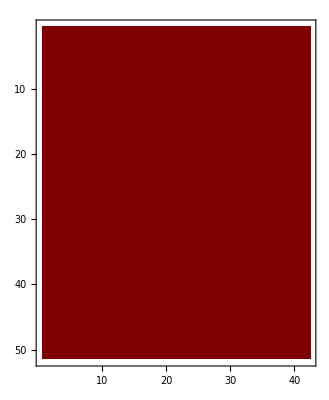
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MatrixPlot[a,PlotTheme->"Scientific"],{a,{okk3new5pc,okk3new2pc,okk3new1pc}}]
```

```mathematica
Vhalo[r]
```

2.89601×10^-8 √(r Rc^2 ρ0 (1/(r (1+r^2/Rc^2))+(1. r)/(r^2+Rc^2)-(r Rc ArcTan[(√(r^2))/Rc])/((r^2)^(3/2))))

```mathematica
Vnet[R]
```

√(8.3869×10^-16 R Rc^2 ρ0 (1/(R (1+R^2/Rc^2))+(1. R)/(R^2+Rc^2)-(R Rc ArcTan[(√(R^2))/Rc])/((R^2)^(3/2)))+(2.09672×10^-16 Σ0 (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)]))/Rd)

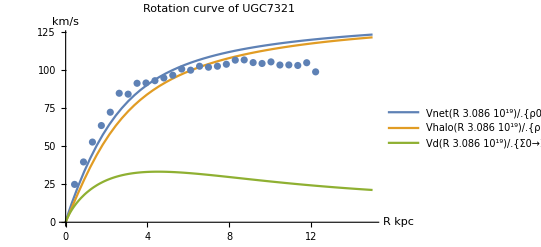

```mathematica
Show[Plot[{Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},Vhalo[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321},Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions"],ListPlot[okoksodata]]
```

```mathematica
(*Show[Plot[{okVnet[R*3.086*10^19]/.{ρ0->(0.080/0.057)*ρUGC7321,Rc->(1.85/2.5)*RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},okVhalo[R*3.086*10^19]/.{ρ0->(0.080/0.057)*ρUGC7321,Rc->(1.85/2.5)*RcUGC7321},Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions"],ListPlot[okoksodata]]*)
```

```mathematica
(*okVhalo[R_]= √(4*N[Pi]*G*ρ0*Rc^2*(1-(Rc/R)ArcTan[R/Rc]))*10^-3*)
```

```mathematica
Vnet[R]
```

√(8.3869×10^-16 R Rc^2 ρ0 (1/(R (1+R^2/Rc^2))+(1. R)/(R^2+Rc^2)-(R Rc ArcTan[(√(R^2))/Rc])/((R^2)^(3/2)))+(2.09672×10^-16 Σ0 (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)]))/Rd)

```mathematica
(*okVnet[R_] = √(Vd[R]^2+okVhalo[R]^2)*)
```

```mathematica
(*Show[Plot[{okVnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},okVhalo[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321},Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions"],ListPlot[okoksodata]]*)
```

### Okdata analysis - Varying halo parameters

```mathematica
Rdata = {0,0.436332,0.872665,1.309,1.74533,2.18166,2.61799,3.05433,3.49066,3.92699,4.36332,4.79966,5.23599,5.67232,6.10865,6.54499,6.98132,7.41765,7.85398,8.29032,8.72665,9.16298,9.59931,10.0356,10.472,10.9083,11.3446,11.781,12.2173}
```

{0,0.436332,0.872665,1.309,1.74533,2.18166,2.61799,3.05433,3.49066,3.92699,4.36332,4.79966,5.23599,5.67232,6.10865,6.54499,6.98132,7.41765,7.85398,8.29032,8.72665,9.16298,9.59931,10.0356,10.472,10.9083,11.3446,11.781,12.2173}

```mathematica
halookVnettest3 = Table[Transpose[Table[Table[Vnet[R*3.086*10^19]/.{ρ0->a,Rc->b,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},{a,ρUGC7321*(0.039/0.057),ρUGC7321,0.01*ρUGC7321}],{R,Drop[Rdata,1]}]],{b,RcUGC7321,RcUGC7321*(2.9/2.5),0.1*10^19}];
```

```mathematica
Dimensions[%113]
```

{1}

```mathematica
okoksodata = {{0.436332,24.85},{0.872665,39.599999999999994},{1.309,52.65},{1.74533,63.5},{2.18166,72.25},{2.61799,84.69999999999999},{3.05433,84.1},{3.49066,91.25},{3.92699,91.44999999999999},{4.36332,92.95},{4.79966,94.75},{5.23599,96.55000000000001},{5.67232,100.6},{6.10865,99.85},{6.54499,102.44999999999999},{6.98132,101.80000000000001},{7.41765,102.45},{7.85398,103.75},{8.29032,106.45},{8.72665,106.6},{9.16298,104.85},{9.59931,104.25},{10.0356,105.3},{10.472,103.25},{10.9083,103.30000000000001},{11.3446,102.94999999999999},{11.781,104.75},{12.2173,98.75}}
```

{{0.436332,24.85},{0.872665,39.6},{1.309,52.65},{1.74533,63.5},{2.18166,72.25},{2.61799,84.7},{3.05433,84.1},{3.49066,91.25},{3.92699,91.45},{4.36332,92.95},{4.79966,94.75},{5.23599,96.55},{5.67232,100.6},{6.10865,99.85},{6.54499,102.45},{6.98132,101.8},{7.41765,102.45},{7.85398,103.75},{8.29032,106.45},{8.72665,106.6},{9.16298,104.85},{9.59931,104.25},{10.0356,105.3},{10.472,103.25},{10.9083,103.3},{11.3446,102.95},{11.781,104.75},{12.2173,98.75}}

```mathematica
oksodata= Flatten[Drop[okoksodata,None,{1}]]
```

{24.85,39.6,52.65,63.5,72.25,84.7,84.1,91.25,91.45,92.95,94.75,96.55,100.6,99.85,102.45,101.8,102.45,103.75,106.45,106.6,104.85,104.25,105.3,103.25,103.3,102.95,104.75,98.75}

```mathematica
okVnettest3[[1]][[1]]
```

okVnettest3

```mathematica
halookk35pc = Table[Table[PearsonChiSquareTest[oksodata,halookVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95],{n,1,32}],{m,1,13}];
```

```mathematica
halookk32pc = Table[Table[PearsonChiSquareTest[oksodata,halookVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.98],{n,1,32}],{m,1,13}];
```

```mathematica
halookk31pc = Table[Table[PearsonChiSquareTest[oksodata,halookVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.99],{n,1,32}],{m,1,13}];
```

```mathematica
halookk3conclusions5pc = Table[Table[halookk35pc[[m]][[n]]["ShortTestConclusion"],{n,1,32}],{m,1,13}];
```

```mathematica
halookk3conclusions2pc = Table[Table[halookk32pc[[m]][[n]]["ShortTestConclusion"],{n,1,32}],{m,1,13}];
```

```mathematica
halookk3conclusions1pc = Table[Table[halookk31pc[[m]][[n]]["ShortTestConclusion"],{n,1,32}],{m,1,13}];
```

```mathematica
halookk3new5pc = halookk3conclusions5pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
halookk3new2pc = halookk3conclusions2pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
halookk3new1pc = halookk3conclusions1pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
For[m=1,m<13,m++,For[n=1,n<32,n++,If[halookk3conclusions5pc[[m]][[n]]== "Do not reject" ,halookk3new5pc[[m]][[n]] = halookk35pc[[m]][[n]]["PValue"],halookk3new5pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<13,m++,For[n=1,n<32,n++,If[halookk3conclusions2pc[[m]][[n]]== "Do not reject" ,halookk3new2pc[[m]][[n]] = halookk32pc[[m]][[n]]["PValue"],halookk3new2pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<13,m++,For[n=1,n<32,n++,If[halookk3conclusions1pc[[m]][[n]]== "Do not reject" ,halookk3new1pc[[m]][[n]] = halookk31pc[[m]][[n]]["PValue"],halookk3new1pc[[m]][[n]] =0]] ]
```

```mathematica
oksodata
```

{24.85,39.6,52.65,63.5,72.25,84.7,84.1,91.25,91.45,92.95,94.75,96.55,100.6,99.85,102.45,101.8,102.45,103.75,106.45,106.6,104.85,104.25,105.3,103.25,103.3,102.95,104.75,98.75}

```mathematica
okoksodata
```

{{0.436332,24.85},{0.872665,39.6},{1.309,52.65},{1.74533,63.5},{2.18166,72.25},{2.61799,84.7},{3.05433,84.1},{3.49066,91.25},{3.92699,91.45},{4.36332,92.95},{4.79966,94.75},{5.23599,96.55},{5.67232,100.6},{6.10865,99.85},{6.54499,102.45},{6.98132,101.8},{7.41765,102.45},{7.85398,103.75},{8.29032,106.45},{8.72665,106.6},{9.16298,104.85},{9.59931,104.25},{10.0356,105.3},{10.472,103.25},{10.9083,103.3},{11.3446,102.95},{11.781,104.75},{12.2173,98.75}}

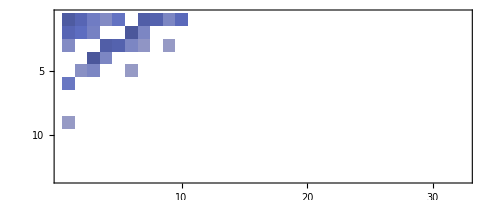
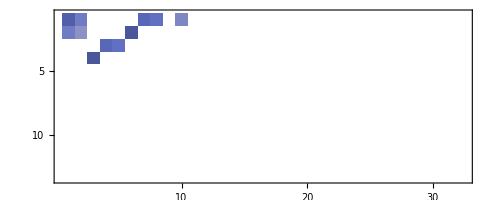
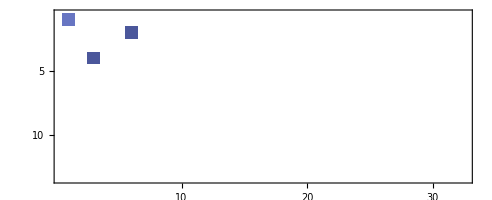

```mathematica
Table[MatrixPlot[a,PlotTheme->"Scientific"],{a,{halookk3new5pc,halookk3new2pc,halookk3new1pc}}]
```

```mathematica
Vhalo[r]
```

2.89601×10^-8 √(r Rc^2 ρ0 (1/(r (1+r^2/Rc^2))+(1. r)/(r^2+Rc^2)-(r Rc ArcTan[(√(r^2))/Rc])/((r^2)^(3/2))))

```mathematica
(*Show[Plot[{okVnet[R*3.086*10^19]/.{ρ0->(0.080/0.057)*ρUGC7321,Rc->(1.85/2.5)*RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},okVhalo[R*3.086*10^19]/.{ρ0->(0.080/0.057)*ρUGC7321,Rc->(1.85/2.5)*RcUGC7321},Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions"],ListPlot[okoksodata]]*)
```

```mathematica
(*okVhalo[R_]= √(4*N[Pi]*G*ρ0*Rc^2*(1-(Rc/R)ArcTan[R/Rc]))*10^-3*)
```

```mathematica
Vnet[R]
```

√(8.3869×10^-16 R Rc^2 ρ0 (1/(R (1+R^2/Rc^2))+(1. R)/(R^2+Rc^2)-(R Rc ArcTan[(√(R^2))/Rc])/((R^2)^(3/2)))+(2.09672×10^-16 Σ0 (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)]))/Rd)

```mathematica
(*okVnet[R_] = √(Vd[R]^2+okVhalo[R]^2)*)
```

```mathematica
(*Show[Plot[{okVnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},okVhalo[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321},Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions"],ListPlot[okoksodata]]*)
```

```mathematica
oksodata
```

{24.85,39.6,52.65,63.5,72.25,84.7,84.1,91.25,91.45,92.95,94.75,96.55,100.6,99.85,102.45,101.8,102.45,103.75,106.45,106.6,104.85,104.25,105.3,103.25,103.3,102.95,104.75,98.75}

```mathematica
{24.85,39.599999999999994,52.65,63.5,72.25,84.69999999999999,84.1,91.25,91.44999999999999,92.95,94.75,96.55000000000001,100.6,99.85,102.44999999999999,101.80000000000001,102.45,103.75,106.45,106.6,104.85,104.25,105.3,103.25,103.30000000000001,102.94999999999999,104.75,98.75}
```

{24.85,39.6,52.65,63.5,72.25,84.7,84.1,91.25,91.45,92.95,94.75,96.55,100.6,99.85,102.45,101.8,102.45,103.75,106.45,106.6,104.85,104.25,105.3,103.25,103.3,102.95,104.75,98.75}

```mathematica
Subscript[Rd, MilkyWay]
```

9.8752×10^19

#### Milkyway

```mathematica
MVnettest = Table[Vnet[R*3.086*10^19]/.{ρ0->ρMilkyway,Rc->RcMilkyway,Σ0->Subscript[Σ, MilkyWay],Rd-> Subscript[Rd, MilkyWay]},{R,0.5,8,0.1}];
```

```mathematica
MVnettest3 = Table[Transpose[Table[Table[Vnet[R*3.086*10^19]/.{ρ0->ρMilkyway,Rc->RcMilkyway,Σ0->a,Rd-> b},{a,3* Subscript[Σ, MilkyWay],4*Subscript[Σ, MilkyWay],0.1*Subscript[Σ, MilkyWay]}],{R,0.5,8,0.1}]],{b, 6* 10^19,11* 10^19,0.1*10^19}];
```

```mathematica
Dimensions[%403]
```

{1}

```mathematica
Dimensions[%401]
```

{1}

#### Chi Squared test

```mathematica
Ck3n = Table[Table[PearsonChiSquareTest[Vnettest,Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95],{n,1,11}],{m,1,51}];
```

```mathematica
MCk3 = Table[Table[PearsonChiSquareTest[MVnettest,MVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95],{n,1,11}],{m,1,51}];
```

```mathematica
MCk32pc = Table[Table[PearsonChiSquareTest[MVnettest,MVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.98],{n,1,11}],{m,1,51}];
```

```mathematica
MCk31pc = Table[Table[PearsonChiSquareTest[MVnettest,MVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.99],{n,1,11}],{m,1,51}];
```

```mathematica
(*Ck3pn = Table[Table[PearsonChiSquareTest[Vnettest,Vnettest3new[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95]["PValue"],{n,1,42}],{m,1,31}];*)
```

```mathematica
MCk3p = Table[Table[PearsonChiSquareTest[MVnettest,MVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95]["PValue"],{n,1,11}],{m,1,51}];
```

```mathematica
MCk3p2pc = Table[Table[PearsonChiSquareTest[MVnettest,MVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.98]["PValue"],{n,1,11}],{m,1,51}];
```

```mathematica
MCk3p1pc = Table[Table[PearsonChiSquareTest[MVnettest,MVnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.99]["PValue"],{n,1,11}],{m,1,51}];
```

```mathematica
MCk3conclusionsn = Table[Table[MCk3n[[m]][[n]]["ShortTestConclusion"],{n,1,11}],{m,1,51}];
```

```mathematica
MCk3conclusions = Table[Table[MCk3[[m]][[n]]["ShortTestConclusion"],{n,1,11}],{m,1,51}];
```

```mathematica
MCk3conclusions2pc = Table[Table[MCk32pc[[m]][[n]]["ShortTestConclusion"],{n,1,11}],{m,1,51}];
```

```mathematica
MCk3conclusions1pc = Table[Table[MCk31pc[[m]][[n]]["ShortTestConclusion"],{n,1,11}],{m,1,51}];
```

```mathematica
MCk3newn = MCk3conclusionsn/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
MCk3new = MCk3conclusions/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
MCk3new2pc = MCk3conclusions2pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
MCk3new1pc = MCk3conclusions1pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
TableForm[MCk3new,TableHeadings->{verticle, horizontal},TableSpacing->{2, 1}];
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<11,n++,If[MCk3conclusionsn[[m]][[n]]== "Do not reject" ,Ck3newn[[m]][[n]] = Ck3pn[[m]][[n]],Ck3newn[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<11,n++,If[MCk3conclusions[[m]][[n]]== "Do not reject" ,MCk3new[[m]][[n]] = MCk3p[[m]][[n]],MCk3new[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<11,n++,If[MCk3conclusions2pc[[m]][[n]]== "Do not reject" ,MCk3new2pc[[m]][[n]] = MCk3p2pc[[m]][[n]],MCk3new2pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<11,n++,If[MCk3conclusions1pc[[m]][[n]]== "Do not reject" ,MCk3new1pc[[m]][[n]] = MCk3p1pc[[m]][[n]],MCk3new1pc[[m]][[n]] =0]] ]
```

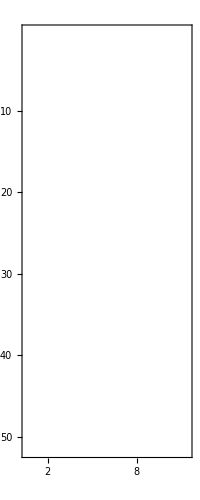
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MatrixPlot[a,PlotTheme->"Scientific"],{a,{MCk3new,MCk3new2pc,MCk3new1pc}}]
```

```mathematica
TableForm[Ck3new,TableHeadings->{verticle, horizontal},TableSpacing->{2, 1}];
```

```mathematica
%124
```

{24.85,39.6,52.65,63.5,72.25,84.7,84.1,91.25,91.45,92.95,94.75,96.55,100.6,99.85,102.45,101.8,102.45,103.75,106.45,106.6,104.85,104.25,105.3,103.25,103.3,102.95,104.75,98.75}

#### F563-1

```mathematica
ρF5631= 0.092* Subscript[M, o] / (3.086*10^16)^3 (* Kg m-3*)
RcF5631 = 1720* 3.086*10^16 (*m*)
```

6.2246×10^-21

5.30792×10^19

```mathematica
μF5631 = 23.6(* mag arcsec-2*)
Subscript[Rd, F5631]= 2800* 3.086*10^16  (*m*)
```

23.6

8.6408×10^19

```mathematica
23.6
```

23.6

```mathematica
μ = -2.5*Log10[Intensity]+24.902
```

24.902-1.08574 Log[Intensity]

```mathematica
Solve[μF5631== -2.5*Log10[Intensity]+21.572+5.48,Intensity]
```

{{Intensity→24.0326}}

```mathematica
24*1.4
```

33.6

```mathematica
ΣF5631 = Intensity*1.4* Subscript[M, o] / (3.086*10^16)^2 (* Kg m-2*)/.{Intensity->24.032558049332412}
```

0.0702502

```mathematica
0.07025020422415913/ (Subscript[M, o] / (3.086*10^16)^2 )
```

33.6456

```mathematica
R2data = {1.5,3,6.6,7.8,9.1,11,13.5,14.15,16.5,17.6}
```

{1.5,3,6.6,7.8,9.1,11,13.5,14.15,16.5,17.6}

```mathematica
{1.5,3,6.6,7.8,9.1,11,13.5,14.15,16.5,17.6}
```

{1.5,3,6.6,7.8,9.1,11,13.5,14.15,16.5,17.6}

```mathematica
Dimensions[R2data]
```

{10}

```mathematica
Vhalo[R]
```

2.89601×10^-8 √(R Rc^2 ρ0 (1/(R (1+R^2/Rc^2))+(1. R)/(R^2+Rc^2)-(R Rc ArcTan[(√(R^2))/Rc])/((R^2)^(3/2))))

```mathematica
okVhalo[R_] = √(4*Pi*G*ρ0*Rc^2(1-(Rc/R)*ArcTan[Rc/R]))*10^-3
```

2.89601×10^-8 √(Rc^2 ρ0 (1-(Rc ArcTan[Rc/R])/R))

```mathematica
okVnet[R_] = √(okVhalo[R]^2+Vd[R]^2)
```

√(8.3869×10^-16 Rc^2 ρ0 (1-(Rc ArcTan[Rc/R])/R)+(2.09672×10^-16 Σ0 (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)]))/Rd)

```mathematica
ok2Vnettest3 = Table[Transpose[Table[Table[okVnet[R*3.086*10^19]/.{ρ0->ρF5631,Rc->RcF5631,Σ0->a,Rd-> b},{a,0,4*ΣF5631,0.01}],{R,Drop[R2data]}]],{b, 4* 10^19,9* 10^19,0.1*10^19}]
```

{{{17.6533,101.579,117.18,118.34,119.117,119.798,120.295,120.383,120.619,120.699},27,{42.0191,110.135,121.792,122.125,122.248,122.282,122.252,122.239,122.188,122.163}},49,{{17.6533,101.579,6,120.619,120.699},27,{1}}}
 |  |  |  |

```mathematica
Dimensions[ok2Vnettest3]
```

{51,29,10}

```mathematica
{51,29,10}
```

{51,29,10}

```mathematica
ok2sodata = {45,81,90,95,100,105,110,110,109,108}
```

{45,81,90,95,100,105,110,110,109,108}

```mathematica
ok2oksodata = {{1.5,45},{3,81},{6.6,90},{7.8,95},{9.1,100},{11,105},{13.5,110},{14.15,110},{16.5,109},{17.6,108}}
```

{{1.5,45},{3,81},{6.6,90},{7.8,95},{9.1,100},{11,105},{13.5,110},{14.15,110},{16.5,109},{17.6,108}}

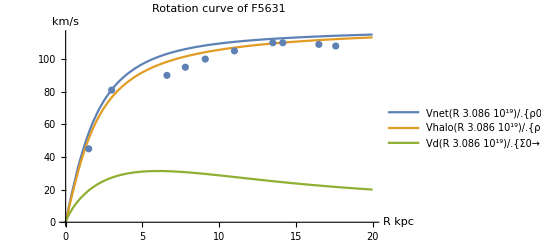

```mathematica
Show[Plot[{Vnet[R*3.086*10^19]/.{ρ0->ρF5631,Rc->RcF5631,Σ0->ΣF5631,Rd-> Subscript[Rd, F5631]},Vhalo[R*3.086*10^19]/.{ρ0->ρF5631,Rc->RcF5631},Vd[R*3.086*10^19]/.{Σ0->ΣF5631,Rd->Subscript[Rd, F5631]}},{R,0,20},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of F5631],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions",PlotRange->All],ListPlot[ok2oksodata]]
```

```mathematica
ok2k35pc = Table[Table[PearsonChiSquareTest[ok2sodata,ok2Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.05],{n,1,29}],{m,1,51}];
```

```mathematica
ok2k32pc = Table[Table[PearsonChiSquareTest[ok2sodata,ok2Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.02],{n,1,29}],{m,1,51}];
```

```mathematica
ok2k31pc = Table[Table[PearsonChiSquareTest[ok2sodata,ok2Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.01],{n,1,29}],{m,1,51}];
```

```mathematica
ok2k3conclusions5pc = Table[Table[ok2k35pc[[m]][[n]]["ShortTestConclusion"],{n,1,29}],{m,1,51}];
```

```mathematica
ok2k3conclusions2pc = Table[Table[ok2k32pc[[m]][[n]]["ShortTestConclusion"],{n,1,29}],{m,1,51}];
```

```mathematica
ok2k3conclusions1pc = Table[Table[ok2k31pc[[m]][[n]]["ShortTestConclusion"],{n,1,29}],{m,1,51}];
```

```mathematica
ok2k3new5pc = ok2k3conclusions5pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
ok2k3new2pc = ok2k3conclusions2pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
ok2k3new1pc = ok2k3conclusions1pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
ArrayPlot[%202]
```

ArrayPlot::mat: Argument %202 at position 1 is not a list of lists.

ArrayPlot[%202]

```mathematica
For[m=1,m<51,m++,For[n=1,n<29,n++,If[ok2k3conclusions5pc[[m]][[n]]== "Do not reject" ,ok2k3new5pc[[m]][[n]] = ok2k35pc[[m]][[n]]["PValue"],ok2k3new5pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<29,n++,If[ok2k3conclusions2pc[[m]][[n]]== "Do not reject" ,ok2k3new2pc[[m]][[n]] = ok2k32pc[[m]][[n]]["PValue"],ok2k3new2pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<29,n++,If[ok2k3conclusions1pc[[m]][[n]]== "Do not reject" ,ok2k3new1pc[[m]][[n]] = ok2k31pc[[m]][[n]]["PValue"],ok2k3new1pc[[m]][[n]] =0]] ]
```

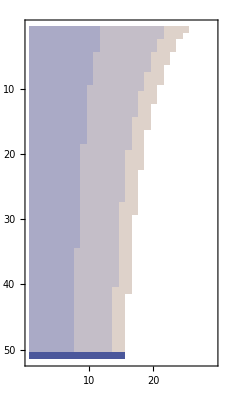
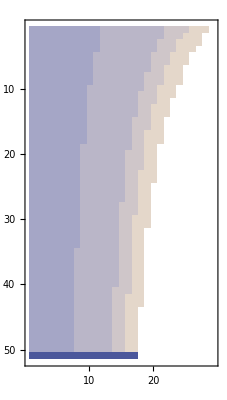
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MatrixPlot[a,PlotTheme->"Scientific"],{a,{ok2k3new5pc,ok2k3new2pc,ok2k3new1pc}}]
```

#### F568-1

```mathematica
ρF5681= 0.0972* Subscript[M, o] / (3.086*10^16)^3 (* Kg m-3*)
RcF5681 = 2220* 3.086*10^16 (*m*)
μF5681 = 23.8(* mag arcsec-2*)
Subscript[Rd, F5681]= 5300* 3.086*10^16  (*m*)
```

6.57643×10^-21

6.85092×10^19

23.8

1.63558×10^20

```mathematica
ρF5681gas = 0.1046 *  Subscript[M, o] / (3.086*10^16)^3 (* Kg m-3*)
RcF5681gas = 2030*3.086*10^16 (*m*)
```

7.0771×10^-21

6.26458×10^19

```mathematica
1.4*^20/(3.086*10^16)
```

4536.62

```mathematica
1.9*^20/(3.086*10^16)
```

6156.84

```mathematica
μ = -2.5*Log10[Intensity]+24.902
```

24.902-1.08574 Log[Intensity]

```mathematica
Solve[μF5681== -2.5*Log10[Intensity]+21.572+5.48,Intensity]
```

{{Intensity→19.9894}}

```mathematica
ΣF5681 = Intensity*1.4* Subscript[M, o] / (3.086*10^16)^2 (* Kg m-2*)/.{{Intensity->19.98941111235659}}
```

{0.0584316}

```mathematica
0.058431574786219416/(Subscript[M, o] / (3.086*10^16)^2 )
```

27.9852

```mathematica
RdataF5681 = {0.4,1.2,2.1,2.9,3.8,4.5,5.2,7.0,7.9,8.6,9.5,12.4}
```

{0.4,1.2,2.1,2.9,3.8,4.5,5.2,7.,7.9,8.6,9.5,12.4}

```mathematica
VdataF5681 = {15,43,68,87,102,109,112,122,125,128,132,141}
```

{15,43,68,87,102,109,112,122,125,128,132,141}

```mathematica
RotdataF5681 = Table[{RdataF5681[[i]],VdataF5681[[i]]},{i,1,12}]
```

{{0.4,15},{1.2,43},{2.1,68},{2.9,87},{3.8,102},{4.5,109},{5.2,112},{7.,122},{7.9,125},{8.6,128},{9.5,132},{12.4,141}}

```mathematica
Dimensions[RdataF5681]
```

{12}

```mathematica
Vnet[R]
```

√(8.3869×10^-16 R Rc^2 ρ0 (1/(R (1+R^2/Rc^2))+(1. R)/(R^2+Rc^2)-(R Rc ArcTan[(√(R^2))/Rc])/((R^2)^(3/2)))+(2.09672×10^-16 Σ0 (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)]))/Rd)

```mathematica
okVhalo[R_] = √(4*Pi*G*ρ0*Rc^2(1-(Rc/R)*ArcTan[Rc/R]))*10^-3
```

2.89601×10^-8 √(Rc^2 ρ0 (1-(Rc ArcTan[Rc/R])/R))

```mathematica
okVnet[R_] = √(okVhalo[R]^2+Vd[R]^2)
```

√(8.3869×10^-16 Rc^2 ρ0 (1-(Rc ArcTan[Rc/R])/R)+(2.09672×10^-16 Σ0 (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)]))/Rd)

```mathematica
Dimensions[VnettestF5681]
```

{}

Halo only fit

```mathematica
FindFit[RotdataF5681,{Vhalo[R*3.086*10^19]/.{ρ0->a*ρF5681,Rc->b*RcF5681}},{a,b},R]
```

{a→0.920976,b→1.04383}

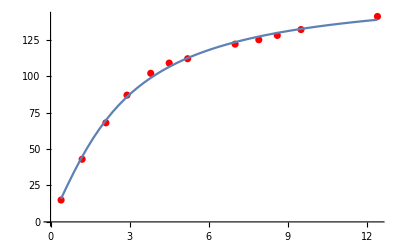

```mathematica
Show[ListPlot[RotdataF5681,PlotStyle->Red],Plot[{Vhalo[R 3.086 10^19]/.{ρ0->a ρF5681,Rc->b RcF5681}}/.{a->0.9209757056465527,b->1.0438257653207152},{R,0.4,12.4}]]
```

```mathematica
a*0.0972
```

0.0972 a

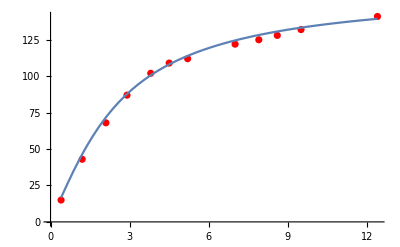

```mathematica
Show[ListPlot[RotdataF5681,PlotStyle->Red],Plot[{Vhalo[R 3.086 10^19]/.{ρ0->ρF5681,Rc->RcF5681}},{R,0.4,12.4}]]
```

```mathematica
a*0.097/.{a->0.83991153450466}
```

0.0814714

```mathematica
b*2.22/.{b->1.0456709887667655}
```

2.32139

```mathematica
a*ρF5681/.{a->0.83991153450466,b->1.0456709887667655}
```

5.52362×10^-21

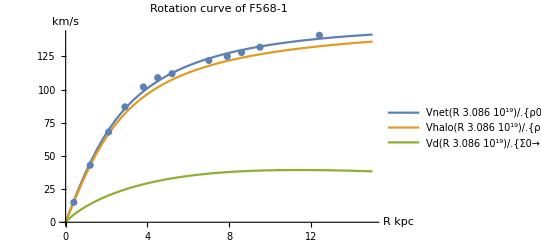

```mathematica
Show[Plot[{Vnet[R*3.086*10^19]/.{ρ0->a*ρF5681,Rc->b*RcF5681,Σ0->ΣF5681,Rd-> Subscript[Rd, F5681]}/.{a->0.83991153450466,b->1.0456709887667655},Vhalo[R*3.086*10^19]/.{ρ0->a*ρF5681,Rc->b*RcF5681}/.{a->0.83991153450466,b->1.0456709887667655},Vd[R*3.086*10^19]/.{Σ0->ΣF5681,Rd->Subscript[Rd, F5681]}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of F568-1],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions"],ListPlot[RotdataF5681]]
```

```mathematica
VnetttestF5681 = Table[Transpose[Table[Table[Vnet[R*3.086*10^19]/.{ρ0->a*ρF5681,Rc->b*RcF5681,Σ0->p,Rd->q}/.{a->0.9209757056465527,b->1.0438257653207152},{p,0,4*ΣF5681[[1]],0.01}],{R,Drop[RdataF5681]}]],{q, 4* 10^19,9* 10^19,0.1*10^19}];
```

```mathematica
Dimensions[%421]
```

{51,24,12}

```mathematica
VnetttestF5681n = Table[Table[Flatten[VnetttestF5681[[m]][[n]]],{n,1,24}],{m,1,151}];
```

```mathematica
Flatten[%208]
```

%208

```mathematica
Dimensions[VnetttestF5681]
```

{151,24,12,1}

```mathematica
VnettestF5681 = Table[Table[Table[{RdataF5681[[p]],VnetttestF5681n[[m]][[n]][[p]]},{p,1,12}],{n,1,24}],{m,1,51}];
```

```mathematica
VnettestF5681[[1]][[10]]
```

{{0.4,17.5465},{1.2,48.3902},{2.1,74.5805},{2.9,91.1938},{3.8,104.636},{4.5,112.462},{5.2,118.674},{7.,129.84},{7.9,133.724},{8.6,136.218},{9.5,138.898},{12.4,144.818}}

```mathematica
Dimensions[VnettestF5681]
```

{51,24,12,2}

```mathematica
KolmogorovSmirnovTest[RotdataF5681,VnettestF5681[[8]][[1]],"HypothesisTestData",SignificanceLevel->0.95]["ShortTestConclusion"]
```

Do not reject

```mathematica
%246["TestDataTable"]
```

%246[TestDataTable]

```mathematica
F5681test5pc = Table[Table[KolmogorovSmirnovTest[RotdataF5681,VnettestF5681[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.90],{n,1,24}],{m,1,51}];
```

```mathematica
F5681test2pc = Table[Table[KolmogorovSmirnovTest[RotdataF5681,VnettestF5681[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.80],{n,1,24}],{m,1,51}];
```

```mathematica
F5681test1pc = Table[Table[KolmogorovSmirnovTest[RotdataF5681,VnettestF5681[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.70],{n,1,24}],{m,1,51}];
```

```mathematica
F5681testconclusions5pc = Table[Table[F5681test5pc[[m]][[n]]["ShortTestConclusion"],{n,1,24}],{m,1,51}];
```

```mathematica
F5681testconclusions2pc = Table[Table[F5681test2pc[[m]][[n]]["ShortTestConclusion"],{n,1,24}],{m,1,51}];
```

```mathematica
F5681testconclusions1pc = Table[Table[F5681test1pc[[m]][[n]]["ShortTestConclusion"],{n,1,24}],{m,1,51}];
```

```mathematica
F5681testnew5pc =F5681testconclusions5pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
F5681testnew2pc =F5681testconclusions2pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
F5681testnew1pc =F5681testconclusions1pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<24,n++,If[F5681testconclusions5pc[[m]][[n]]== "Do not reject" ,F5681testnew5pc[[m]][[n]] = F5681test5pc[[m]][[n]]["PValue"],F5681testnew5pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<24,n++,If[F5681testconclusions2pc[[m]][[n]]== "Do not reject" ,F5681testnew2pc[[m]][[n]] =F5681test2pc[[m]][[n]]["PValue"],F5681testnew2pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<24,n++,If[F5681testconclusions1pc[[m]][[n]]== "Do not reject" ,F5681testnew1pc[[m]][[n]] =F5681test1pc[[m]][[n]]["PValue"],F5681testnew1pc[[m]][[n]] =0]] ]
```

```mathematica
Dimensions[F5681testnew1pc]
```

{51,24}

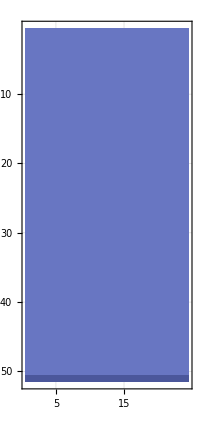
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MatrixPlot[a,PlotTheme->"Scientific",GridLines->Automatic],{a,{F5681testnew5pc,F5681testnew2pc,F5681testnew1pc}}]
```

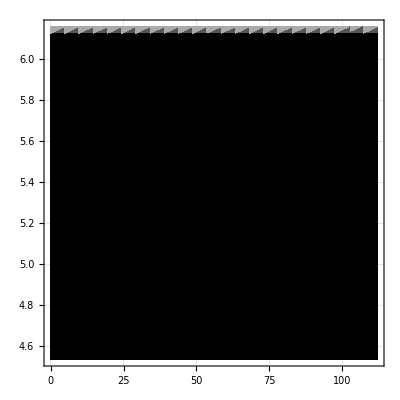
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListDensityPlot[a,DataRange->{{0,112},{4.536,6.16},InterpolationOrder->0},GridLines->Automatic,ColorFunction->GrayLevel],{a,{F5681testnew5pc,F5681testnew2pc,F5681testnew1pc}}]
```

```mathematica
4*ΣF5681
```

{0.233726}

```mathematica
4*27.98
```

111.92

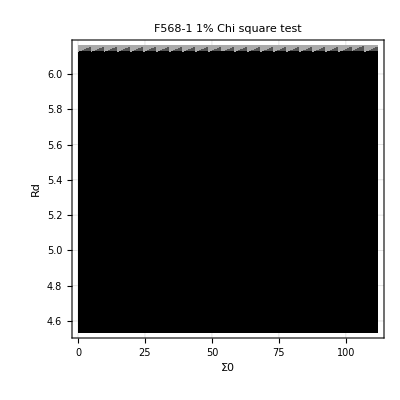

```mathematica
Show[ListDensityPlot[F5681testnew1pc,DataRange->{{0,112},{4.536,6.16},InterpolationOrder->0},GridLines->Automatic,ColorFunction->GrayLevel],FrameLabel->{{HoldForm[Rd],None},{HoldForm[Σ0],None}},PlotLabel->HoldForm["F568-1 1% Chi square test"],LabelStyle->{FontFamily->"Lato",GrayLevel[0]}]
```

#### F574-1

```mathematica
ρF5741= 0.153* Subscript[M, o] / (3.086*10^16)^3 (* Kg m-3*)
RcF5741 = 1450* 3.086*10^16 (*m*)
μF5741 = 23.3(* mag arcsec-2*)
Subscript[Rd, F5741]= 4300* 3.086*10^16  (*m*)
```

1.03518×10^-20

4.4747×10^19

23.3

1.32698×10^20

```mathematica
1.5*^20/ (3.086*10^16)
```

4860.66

```mathematica
μ = -2.5*Log10[Intensity]+24.902
```

24.902-1.08574 Log[Intensity]

Converting Mass to light ratio to intensity

```mathematica
Solve[μF5741== -2.5*Log10[Intensity]+21.572+5.48,Intensity]
```

{{Intensity→31.6811}}

Getting the Surface brightness density from the intensity

```mathematica
ΣF5741 = Intensity*1.4* Subscript[M, o] / (3.086*10^16)^2 (* Kg m-2*)/.{{Intensity->31.681081593280496}}
```

{0.0926078}

```mathematica
0.0926078051034616/(Subscript[M, o] / (3.086*10^16)^2 )
```

44.3535

Radius data points

```mathematica
RdataF5741 = {0.5,1.4,2.3,3.2,4.1,5.0,6.0,7.0,7.9,8.9,9.8,10.7,11.6,12.4}
```

{0.5,1.4,2.3,3.2,4.1,5.,6.,7.,7.9,8.9,9.8,10.7,11.6,12.4}

Velocity data points

```mathematica
VdataF5741 = {15,40,60,75,83,85,87,92,93,95,96,97,98,99}
```

{15,40,60,75,83,85,87,92,93,95,96,97,98,99}

```mathematica
RotdataF5741 = Table[{RdataF5741[[i]],VdataF5741[[i]]},{i,1,14}]
```

{{0.5,15},{1.4,40},{2.3,60},{3.2,75},{4.1,83},{5.,85},{6.,87},{7.,92},{7.9,93},{8.9,95},{9.8,96},{10.7,97},{11.6,98},{12.4,99}}

```mathematica
Dimensions[RdataF5741]
```

{14}

```mathematica
Dimensions[VdataF5741]
```

{14}

Fitting for (halo+disk) potential to get halo parameters

{a→0.363746,b→1.25353}

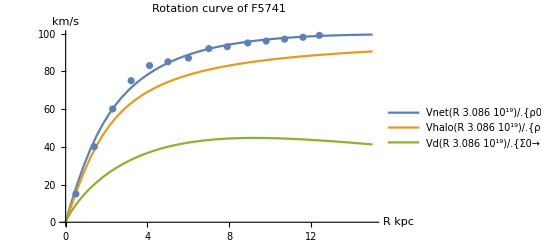

```mathematica
FindFit[RotdataF5741,{Vnet[R*3.086*10^19]/.{Σ0->ΣF5741,Rd-> Subscript[Rd, F5741],ρ0->a*ρF5741,Rc->b*RcF5741}},{a,b},R]
```

Fitting for Halo only potential

```mathematica
FindFit[RotdataF5741,{Vhalo[R*3.086*10^19]/.{Σ0->ΣF5741,Rd-> Subscript[Rd, F5741],ρ0->a*ρF5741,Rc->b*RcF5741}},{a,b},R]
```

{a→0.476384,b→1.23022}

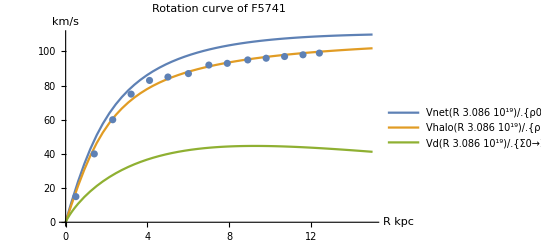

```mathematica
Show[Plot[{Vnet[R*3.086*10^19]/.{ρ0->a*ρF5741,Rc->b*RcF5741,Σ0->ΣF5741,Rd-> Subscript[Rd, F5741]}/.{a->0.47638368992556007,b->1.2302210309420434},Vhalo[R*3.086*10^19]/.{ρ0->a*ρF5741,Rc->b*RcF5741}/.{a->0.47638368992556007,b->1.2302210309420434},Vd[R*3.086*10^19]/.{Σ0->ΣF5741,Rd->Subscript[Rd, F5741]}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of F5741],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions"],ListPlot[RotdataF5741]]
```

```mathematica
VnetttestF5741= Table[Transpose[Table[Table[Vnet[R*3.086*10^19]/.{ρ0->a ρUGC7321,Rc->b RcUGC7321,Σ0->p,Rd-> q}/.{a->0.47638368992556007,b->1.2302210309420434},{p,0,4*ΣF5741[[1]],0.01}],{R,RdataF5741}]],{q, 4* 10^19,9* 10^19,0.1*10^19}];
```

```mathematica
Dimensions[VnetttestF5741]
```

{51,38,14}

```mathematica
Dimensions[RotdataF5741]
```

{14,2}

```mathematica
VnettestF5741 = Table[Table[Table[{RdataF5741[[p]],VnetttestF5741[[m]][[n]][[p]]},{p,1,14}],{n,1,38}],{m,1,51}];
```

```mathematica
Dimensions[VnettestF5741]
```

{51,38,14,2}

```mathematica
VnettestF5741[[1]][[1]]
```

{{0.5,10.9718},{1.4,29.2356},{2.3,44.297},{3.2,56.0192},{4.1,65.0082},{5.,71.9528},{6.,77.9376},{7.,82.6156},{7.9,86.0129},{8.9,89.1162},{9.8,91.4461},{10.7,93.434},{11.6,95.1486},{12.4,96.4853}}

{51,38}

{51,42}

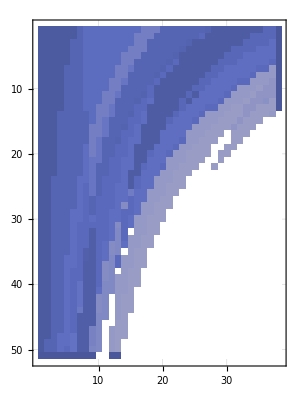
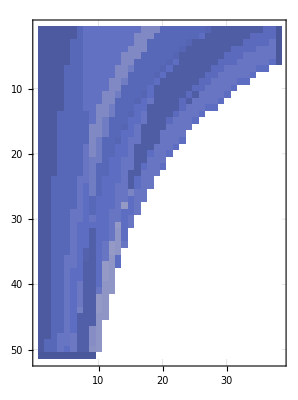
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
F5741test5pc = Table[Table[PearsonChiSquareTest[RotdataF5741,VnettestF5741[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95],{n,1,38}],{m,1,51}];
F5741test2pc = Table[Table[PearsonChiSquareTest[RotdataF5741,VnettestF5741[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.98],{n,1,38}],{m,1,51}];
F5741test1pc = Table[Table[PearsonChiSquareTest[RotdataF5741,VnettestF5741[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.99],{n,1,38}],{m,1,51}];
F5741testconclusions5pc = Table[Table[F5741test5pc[[m]][[n]]["ShortTestConclusion"],{n,1,38}],{m,1,51}];
F5741testconclusions2pc = Table[Table[F5741test2pc[[m]][[n]]["ShortTestConclusion"],{n,1,38}],{m,1,51}];
F5741testconclusions1pc = Table[Table[F5741test1pc[[m]][[n]]["ShortTestConclusion"],{n,1,38}],{m,1,51}];
F5741testnew5pc =F5741testconclusions5pc/.{"Do not reject" -> 1,"Reject"-> 0};
F5741testnew2pc =F5741testconclusions2pc/.{"Do not reject" -> 1,"Reject"-> 0};
F5741testnew1pc =F5741testconclusions1pc/.{"Do not reject" -> 1,"Reject"-> 0};

For[m=1,m<51,m++,For[n=1,n<38,n++,If[F5741testconclusions5pc[[m]][[n]]== "Do not reject" ,F5741testnew5pc[[m]][[n]] = F5741test5pc[[m]][[n]]["PValue"],F5741testnew5pc[[m]][[n]] =0]] ]
For[m=1,m<51,m++,For[n=1,n<38,n++,If[F5741testconclusions2pc[[m]][[n]]== "Do not reject" ,F5741testnew2pc[[m]][[n]] =F5741test2pc[[m]][[n]]["PValue"],F5741testnew2pc[[m]][[n]] =0]] ]
For[m=1,m<51,m++,For[n=1,n<38,n++,If[F5741testconclusions1pc[[m]][[n]]== "Do not reject" ,F5741testnew1pc[[m]][[n]] =F5741test1pc[[m]][[n]]["PValue"],F5741testnew1pc[[m]][[n]] =0]] ]
Dimensions[F5741testnew1pc]
{51,42}

Table[MatrixPlot[a,PlotTheme->"Scientific",GridLines->Automatic],{a,{F5741testnew5pc,F5741testnew2pc,F5741testnew1pc}}]
```

```mathematica
Table[MatrixPlot[a,PlotTheme->"Scientific",GridLines->Automatic],{a,{F5741testnew5pc,F5741testnew2pc,F5741testnew1pc}}]
```

{-Graphics-,-Graphics-,-Graphics-}

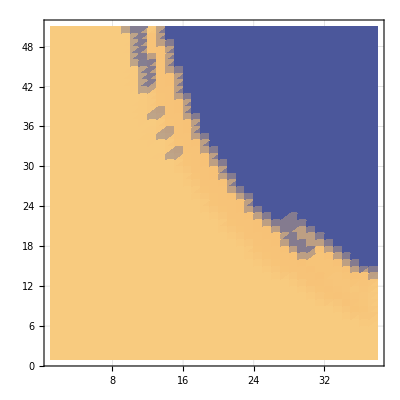
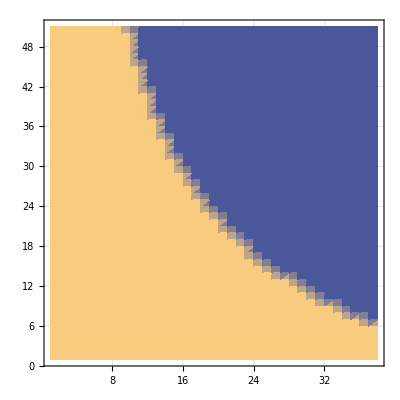
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListDensityPlot[a,PlotTheme->"Scientific",GridLines->Automatic],{a,{F5741testnew5pc,F5741testnew2pc,F5741testnew1pc}}]
```

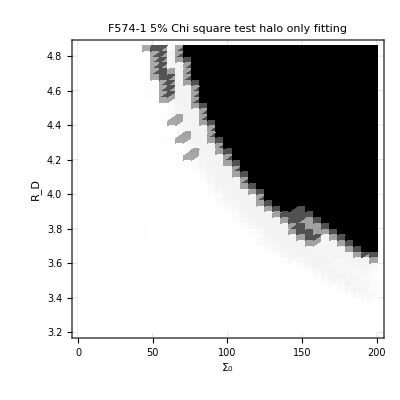

```mathematica
Show[ListDensityPlot[F5741testnew5pc,DataRange->{{0,200.8},{3.2,4.86},InterpolationOrder->0},GridLines->Automatic,ColorFunction->GrayLevel],FrameLabel->{{HoldForm[Subscript[R, D]],None},{HoldForm[Subscript[Σ, 0]],None}},PlotLabel->HoldForm["F574-1 5% Chi square test halo only fitting"],LabelStyle->{FontFamily->"Lato",GrayLevel[0]}]
```

{51,38}

{51,42}

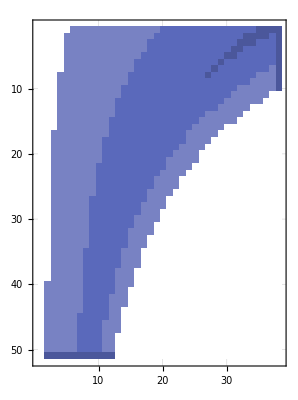
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
F5741test5pc = Table[Table[KolmogorovSmirnovTest[RotdataF5741,VnettestF5741[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95],{n,1,38}],{m,1,51}];
F5741test2pc = Table[Table[KolmogorovSmirnovTest[RotdataF5741,VnettestF5741[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.98],{n,1,38}],{m,1,51}];
F5741test1pc = Table[Table[KolmogorovSmirnovTest[RotdataF5741,VnettestF5741[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.99],{n,1,38}],{m,1,51}];
F5741testconclusions5pc = Table[Table[F5741test5pc[[m]][[n]]["ShortTestConclusion"],{n,1,38}],{m,1,51}];
F5741testconclusions2pc = Table[Table[F5741test2pc[[m]][[n]]["ShortTestConclusion"],{n,1,38}],{m,1,51}];
F5741testconclusions1pc = Table[Table[F5741test1pc[[m]][[n]]["ShortTestConclusion"],{n,1,38}],{m,1,51}];
F5741testnew5pc =F5741testconclusions5pc/.{"Do not reject" -> 1,"Reject"-> 0};
F5741testnew2pc =F5741testconclusions2pc/.{"Do not reject" -> 1,"Reject"-> 0};
F5741testnew1pc =F5741testconclusions1pc/.{"Do not reject" -> 1,"Reject"-> 0};

For[m=1,m<51,m++,For[n=1,n<38,n++,If[F5741testconclusions5pc[[m]][[n]]== "Do not reject" ,F5741testnew5pc[[m]][[n]] = F5741test5pc[[m]][[n]]["PValue"],F5741testnew5pc[[m]][[n]] =0]] ]
For[m=1,m<51,m++,For[n=1,n<38,n++,If[F5741testconclusions2pc[[m]][[n]]== "Do not reject" ,F5741testnew2pc[[m]][[n]] =F5741test2pc[[m]][[n]]["PValue"],F5741testnew2pc[[m]][[n]] =0]] ]
For[m=1,m<51,m++,For[n=1,n<38,n++,If[F5741testconclusions1pc[[m]][[n]]== "Do not reject" ,F5741testnew1pc[[m]][[n]] =F5741test1pc[[m]][[n]]["PValue"],F5741testnew1pc[[m]][[n]] =0]] ]
Dimensions[F5741testnew1pc]
{51,42}

Table[MatrixPlot[a,PlotTheme->"Scientific",GridLines->Automatic],{a,{F5741testnew5pc,F5741testnew2pc,F5741testnew1pc}}]
```

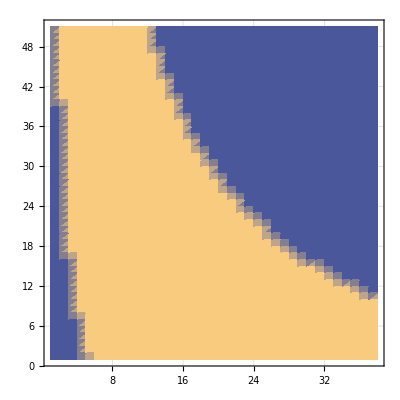
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListDensityPlot[a,PlotTheme->"Scientific",GridLines->Automatic],{a,{F5741testnew5pc,F5741testnew2pc,F5741testnew1pc}}]
```

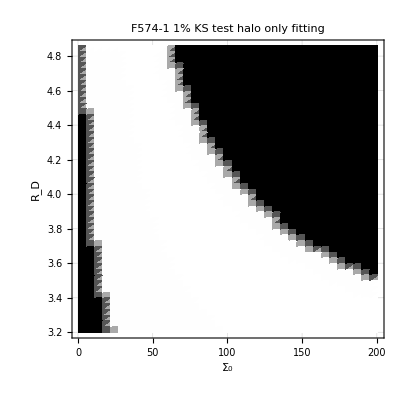

```mathematica
Show[ListDensityPlot[F5741testnew1pc,DataRange->{{0,200.8},{3.2,4.86},InterpolationOrder->0},GridLines->Automatic,ColorFunction->GrayLevel],FrameLabel->{{HoldForm[Subscript[R, D]],None},{HoldForm[Subscript[Σ, 0]],None}},PlotLabel->HoldForm["F574-1 1% KS test halo only fitting"],LabelStyle->{FontFamily->"Lato",GrayLevel[0]}]
```

#### F568-3

```mathematica
ρF5683= 0.037* Subscript[M, o] / (3.086*10^16)^3 (* Kg m-3*)
RcF5683 = 2920* 3.086*10^16 (*m*)
```

2.50337×10^-21

9.01112×10^19

```mathematica
μF5683 = 23.1(* mag arcsec-2*)
Subscript[Rd, F5683]= 4000* 3.086*10^16  (*m*)
```

23.1

1.2344×10^20

```mathematica
Solve[μF5683== -2.5*Log10[Intensity1]+21.572+5.48,Intensity1]
```

{{Intensity1→38.089}}

```mathematica
38.1*1.4
```

53.34

```mathematica
ΣF5683 = Intensity1*1.4* Subscript[M, o] / (3.086*10^16)^2 (* Kg m-2*)/.{Intensity1->38.08903764981348}
```

0.111339

```mathematica
Subscript[Σ, UGC7321]
```

0.104815

```mathematica
R3data = {0.47,1.15,1.9,2.75,3.41,4.15,4.9,5.6,6.1,7.08,9.0,9.5,11.25}
```

{0.47,1.15,1.9,2.75,3.41,4.15,4.9,5.6,6.1,7.08,9.,9.5,11.25}

```mathematica
Dimensions[R3data]
```

{13}

```mathematica
Drop[R3data]
```

{0.47,1.15,1.9,2.75,3.41,4.15,4.9,5.6,6.1,7.08,9.,9.5,11.25}

```mathematica
ok3Vnettest3 = Table[Transpose[Table[Table[Vnet[R*3.086*10^19]/.{ρ0->ρF5683,Rc->RcF5683,Σ0->a,Rd-> b},{a,0,4*ΣF5683,0.01}],{R,Drop[R3data]}]],{b, 4* 10^19,9* 10^19,0.1*10^19}]
```

{{{12.0408,28.417,43.9813,58.0816,66.7447,74.5717,80.9308,85.7757,88.7287,93.5638,100.475,101.882,105.931},43,{28.5337,51.5978,67.4275,78.9286,85.0566,90.139,94.0549,96.9822,98.772,101.762,106.296,107.27,110.189}},49,{1}}
 |  |  |  |

```mathematica
Dimensions[ok3Vnettest3]
```

{51,45,13}

```mathematica
ok3sodata = {5,20,33,47,62,80,91,100,101,99,95,96,96}
```

{5,20,33,47,62,80,91,100,101,99,95,96,96}

```mathematica
Dimensions[ok3sodata]
```

{13}

```mathematica
ok3oksodata={{0.47,5},{1.15,20},{1.9,33},{2.75,47},{3.41,62},{4.15,80},{4.9,91},{5.6,100},{6.1,101},{7.08,99},{9.0,95},{9.5,96},{11.25,96}}
```

{{0.47,5},{1.15,20},{1.9,33},{2.75,47},{3.41,62},{4.15,80},{4.9,91},{5.6,100},{6.1,101},{7.08,99},{9.,95},{9.5,96},{11.25,96}}

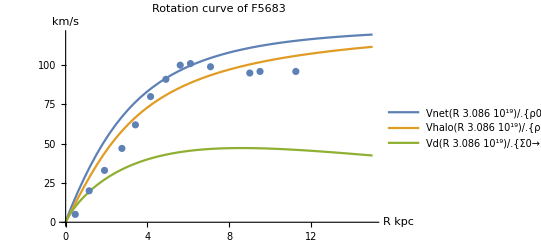

```mathematica
Show[Plot[{Vnet[R*3.086*10^19]/.{ρ0->ρF5683,Rc->RcF5683,Σ0->ΣF5683,Rd-> Subscript[Rd, F5683]},Vhalo[R*3.086*10^19]/.{ρ0->ρF5683,Rc->RcF5683},Vd[R*3.086*10^19]/.{Σ0->ΣF5683,Rd->Subscript[Rd, F5683]}},{R,0,15},AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of F5683],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions"],ListPlot[ok3oksodata]]
```

```mathematica
ok3k35pc = Table[Table[PearsonChiSquareTest[ok3sodata,ok3Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95],{n,1,29}],{m,1,51}];
```

```mathematica
ok3k32pc = Table[Table[PearsonChiSquareTest[ok3sodata,ok3Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.98],{n,1,29}],{m,1,51}];
```

```mathematica
ok3k31pc = Table[Table[PearsonChiSquareTest[ok3sodata,ok3Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.99],{n,1,29}],{m,1,51}];
```

```mathematica
ok3k3conclusions5pc = Table[Table[ok3k35pc[[m]][[n]]["ShortTestConclusion"],{n,1,29}],{m,1,51}];
```

```mathematica
ok3k3conclusions2pc = Table[Table[ok3k32pc[[m]][[n]]["ShortTestConclusion"],{n,1,29}],{m,1,51}];
```

```mathematica
ok3k3conclusions1pc = Table[Table[ok3k31pc[[m]][[n]]["ShortTestConclusion"],{n,1,29}],{m,1,51}];
```

```mathematica
ok3k3new5pc = ok3k3conclusions5pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
ok3k3new2pc = ok3k3conclusions2pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
ok3k3new1pc = ok3k3conclusions1pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<29,n++,If[ok3k3conclusions5pc[[m]][[n]]== "Do not reject" ,ok3k3new5pc[[m]][[n]] = ok3k35pc[[m]][[n]]["PValue"],ok3k3new5pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<29,n++,If[ok3k3conclusions2pc[[m]][[n]]== "Do not reject" ,ok3k3new2pc[[m]][[n]] = ok3k32pc[[m]][[n]]["PValue"],ok3k3new2pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<29,n++,If[ok3k3conclusions1pc[[m]][[n]]== "Do not reject" ,ok3k3new1pc[[m]][[n]] = ok3k31pc[[m]][[n]]["PValue"],ok3k3new1pc[[m]][[n]] =0]] ]
```

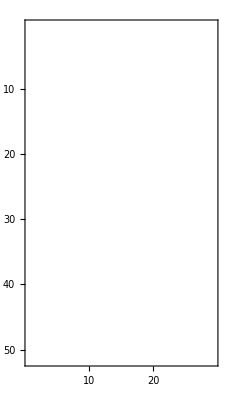
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MatrixPlot[a,PlotTheme->"Scientific"],{a,{ok3k3new5pc,ok3k3new2pc,ok3k3new1pc}}]
```

```mathematica
aok3k35pc = Table[Table[AndersonDarlingTest[ok3sodata,ok3Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.05],{n,1,29}],{m,1,51}];
```

```mathematica
aok3k32pc = Table[Table[AndersonDarlingTest[ok3sodata,ok3Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.02],{n,1,29}],{m,1,51}];
```

```mathematica
aok3k31pc = Table[Table[AndersonDarlingTest[ok3sodata,ok3Vnettest3[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.01],{n,1,29}],{m,1,51}];
```

```mathematica
aok3k3conclusions5pc = Table[Table[aok3k35pc[[m]][[n]]["ShortTestConclusion"],{n,1,29}],{m,1,51}];
```

```mathematica
aok3k3conclusions2pc = Table[Table[aok3k32pc[[m]][[n]]["ShortTestConclusion"],{n,1,29}],{m,1,51}];
```

```mathematica
aok3k3conclusions1pc = Table[Table[aok3k31pc[[m]][[n]]["ShortTestConclusion"],{n,1,29}],{m,1,51}];
```

```mathematica
aok3k3new5pc = aok3k3conclusions5pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
aok3k3new2pc = aok3k3conclusions2pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
aok3k3new1pc = aok3k3conclusions1pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<29,n++,If[aok3k3conclusions5pc[[m]][[n]]== "Do not reject" ,aok3k3new5pc[[m]][[n]] = aok3k35pc[[m]][[n]]["PValue"],aok3k3new5pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<29,n++,If[aok3k3conclusions2pc[[m]][[n]]== "Do not reject" ,aok3k3new2pc[[m]][[n]] = aok3k32pc[[m]][[n]]["PValue"],aok3k3new2pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<29,n++,If[aok3k3conclusions1pc[[m]][[n]]== "Do not reject" ,aok3k3new1pc[[m]][[n]] = aok3k31pc[[m]][[n]]["PValue"],aok3k3new1pc[[m]][[n]] =0]] ]
```

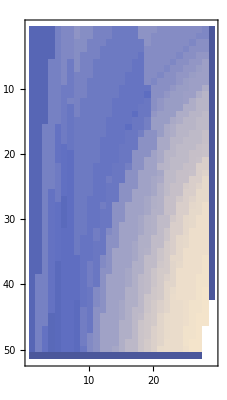
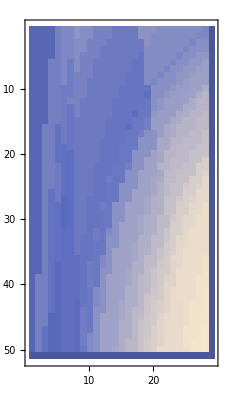
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MatrixPlot[a,PlotTheme->"Scientific"],{a,{aok3k3new5pc,aok3k3new2pc,aok3k3new1pc}}]
```

1. Doing Chi square fits to UGC7321 data and getting the halo parameters and then doing the Chi-square fit for the same and obtaining the range of allowed halo parameters
2. Doing the chi-square fitting for 10% and 15%
3. similar tests for other galaxies given in deBlok paper.

#### UGC7321

```mathematica
Rdata = {0,0.436332,0.872665,1.309,1.74533,2.18166,2.61799,3.05433,3.49066,3.92699,4.36332,4.79966,5.23599,5.67232,6.10865,6.54499,6.98132,7.41765,7.85398,8.29032,8.72665,9.16298,9.59931,10.0356,10.472,10.9083,11.3446,11.781,12.2173}
```

{0,0.436332,0.872665,1.309,1.74533,2.18166,2.61799,3.05433,3.49066,3.92699,4.36332,4.79966,5.23599,5.67232,6.10865,6.54499,6.98132,7.41765,7.85398,8.29032,8.72665,9.16298,9.59931,10.0356,10.472,10.9083,11.3446,11.781,12.2173}

Data of the radial points

```mathematica
RdataUGC7321 = Drop[Rdata,1]
```

{0.436332,0.872665,1.309,1.74533,2.18166,2.61799,3.05433,3.49066,3.92699,4.36332,4.79966,5.23599,5.67232,6.10865,6.54499,6.98132,7.41765,7.85398,8.29032,8.72665,9.16298,9.59931,10.0356,10.472,10.9083,11.3446,11.781,12.2173}

```mathematica
ρUGC7321
```

3.85655×10^-21

```mathematica
RcUGC7321
```

7.715×10^19

```mathematica
Subscript[Σ, UGC7321] = 50.2 * Subscript[M, o] / (3.086*10^16)^2 (* Kg m-2*)
Subscript[Rd, UGC7321]= 2100* 3.086*10^16  (*m*)
```

0.104815

6.4806×10^19

```mathematica
Vnet[R]
```

√(8.3869×10^-16 R Rc^2 ρ0 (1/(R (1+R^2/Rc^2))+(1. R)/(R^2+Rc^2)-(R Rc ArcTan[(√(R^2))/Rc])/((R^2)^(3/2)))+(2.09672×10^-16 Σ0 (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)]))/Rd)

```mathematica
Dimensions[RotdataUGC7321]
```

{}

Radius versus rotation velocity

```mathematica
RotdataUGC7321 = {{0.436332,24.85},{0.872665,39.599999999999994},{1.309,52.65},{1.74533,63.5},{2.18166,72.25},{2.61799,84.69999999999999},{3.05433,84.1},{3.49066,91.25},{3.92699,91.44999999999999},{4.36332,92.95},{4.79966,94.75},{5.23599,96.55000000000001},{5.67232,100.6},{6.10865,99.85},{6.54499,102.44999999999999},{6.98132,101.80000000000001},{7.41765,102.45},{7.85398,103.75},{8.29032,106.45},{8.72665,106.6},{9.16298,104.85},{9.59931,104.25},{10.0356,105.3},{10.472,103.25},{10.9083,103.30000000000001},{11.3446,102.94999999999999},{11.781,104.75},{12.2173,98.75}}
```

{{0.436332,24.85},{0.872665,39.6},{1.309,52.65},{1.74533,63.5},{2.18166,72.25},{2.61799,84.7},{3.05433,84.1},{3.49066,91.25},{3.92699,91.45},{4.36332,92.95},{4.79966,94.75},{5.23599,96.55},{5.67232,100.6},{6.10865,99.85},{6.54499,102.45},{6.98132,101.8},{7.41765,102.45},{7.85398,103.75},{8.29032,106.45},{8.72665,106.6},{9.16298,104.85},{9.59931,104.25},{10.0356,105.3},{10.472,103.25},{10.9083,103.3},{11.3446,102.95},{11.781,104.75},{12.2173,98.75}}

Fitting the data points for the potential due to halo only.

```mathematica
FindFit[RotdataUGC7321,Vhalo[R*3.086*10^19]/.{ρ0->p*ρUGC7321,Rc->q*RcUGC7321},{p,q},R]
```

{p→2.96282,q→0.484948}

```mathematica
p*0.057/.{p->2.9628184081392925,q->0.4849475591079378}
```

0.168881

```mathematica
q*2.5/.{p->2.9628184081392925,q->0.4849475591079378}
```

1.21237

Hence halo parameters for halo only fit is ρ0 = 0.168881, Rc = 1.21237
Halo parameters for halo+disk fit gives ρ0 = 0.125678 , Rc = 1.36765

```mathematica
a*0.057/.{a->2.2048804456029933,b->0.5470606485101092}
```

0.125678

```mathematica
b*2.5/.{a->2.2048804456029933,b->0.5470606485101092}
```

1.36765

```mathematica
FindFit[RotdataUGC7321,{Vnet[R*3.086*10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321],ρ0->a*ρUGC7321,Rc->b*RcUGC7321}},{a,b},R]
```

{a→2.20488,b→0.547061}

```mathematica
b*2.5/.{b->0.5470606485101092}
```

1.36765

```mathematica
Show[Plot[Vnet[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},{R,0,15},Frame-> True,FrameLabel->{HoldForm["R (kpc)"],HoldForm["Rotation Velocity " "(km s^-1)"]},LabelStyle->Directive[Black,FontSize->12],PlotLabel->HoldForm[UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions",PlotLabels->Placed["vnet",Above],PlotStyle->Gray],
Plot[Vhalo[R*3.086*10^19]/.{ρ0->ρUGC7321,Rc->RcUGC7321},{R,0,15},Frame-> True,FrameLabel->{HoldForm["R (kpc)"],HoldForm["Rotation Velocity " "(km s^-1)"]},LabelStyle->Directive[Black,FontSize->12],PlotLabel->HoldForm[UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions",PlotLabels->Placed["vhalo",{Scaled[1.,80],Below}],PlotStyle->Dashed],
Plot[Vd[R*3.086*10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]},{R,0,15},Frame-> True,FrameLabel->{HoldForm["R (kpc)"],HoldForm["Rotation Velocity " "(km s^-1)"]},LabelStyle->Directive[Black,FontSize->12],PlotLabel->HoldForm[UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions",PlotLabels->Placed[{"vd"},Above],PlotStyle->Dotted]]
```

-Graphics-

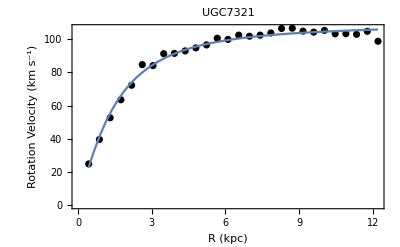

```mathematica
Show[ListPlot[RotdataUGC7321,PlotStyle->Black],Plot[{Vnet[R 3.086 10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd->Subscript[Rd, UGC7321],ρ0->a ρUGC7321,Rc->b RcUGC7321}}/.{a->2.2048804456029933,b->0.5470606485101092},{R,0.436332,12.2173}],FrameLabel->{HoldForm["R (kpc)"],HoldForm["Rotation Velocity " "(km s^-1)"]},LabelStyle->Directive[Black,FontSize->12],PlotLabel->HoldForm[UGC7321],LabelStyle->{GrayLevel[0]},Frame->True]
```

```mathematica
Show[%45,AxesLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[UGC7321],LabelStyle->{FontFamily->"STIXIntegralsUp",GrayLevel[0]}]
```

Show::gcomb: Could not combine the graphics objects in Show[«1»].

Show[{{{15.8335,18.9041,21.9248,24.8896,27.7929,30.6304,33.398,36.093,38.7131,41.2568,43.7232,46.1121,52,103.536,103.972,104.397,104.812,105.218,105.614,106.002,106.38,106.751,107.113,107.467,107.814},40,{1}},50},3]
 |  |  |  |

```mathematica
VnetfitUGC7321 = Table[{R,Vnet[R*3.086*10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd->Subscript[Rd, UGC7321],ρ0->a ρUGC7321,Rc->b RcUGC7321}/.{a->2.2048804456029933,b->0.5470606485101092}},{R,RdataUGC7321}]
```

{{0.436332,22.8796},{0.872665,41.2934},{1.309,55.433},{1.74533,66.0151},{2.18166,73.9546},{2.61799,79.9938},{3.05433,84.6625},{3.49066,88.3275},{3.92699,91.2446},{4.36332,93.5951},{4.79966,95.5101},{5.23599,97.086},{5.67232,98.3953},{6.10865,99.493},{6.54499,100.422},{6.98132,101.214},{7.41765,101.896},{7.85398,102.488},{8.29032,103.007},{8.72665,103.464},{9.16298,103.871},{9.59931,104.236},{10.0356,104.566},{10.472,104.866},{10.9083,105.14},{11.3446,105.392},{11.781,105.626},{12.2173,105.843}}

```mathematica
Drop[VnetfitUGC7321,None,{1}]
```

{{22.8796},{41.2934},{55.433},{66.0151},{73.9546},{79.9938},{84.6625},{88.3275},{91.2446},{93.5951},{95.5101},{97.086},{98.3953},{99.493},{100.422},{101.214},{101.896},{102.488},{103.007},{103.464},{103.871},{104.236},{104.566},{104.866},{105.14},{105.392},{105.626},{105.843}}

Table for (halo only) best fit parameters

```mathematica
VnetttestUGC7321= Table[Transpose[Table[Table[Vnet[R*3.086*10^19]/.{ρ0->a ρUGC7321,Rc->b RcUGC7321,Σ0->p,Rd-> q}/.{a->2.9628184081392925,b->0.4849475591079378},{p,0,4*Subscript[Σ, UGC7321],0.01}],{R,RdataUGC7321}]],{q, 4* 10^19,9* 10^19,0.1*10^19}];
```

```mathematica
Dimensions[VnetttestUGC7321]
```

{51,42,28}

```mathematica
horizontal = Table[j,{j,0,4*Subscript[Σ, UGC7321],0.01}]/(Subscript[M, o] / (3.086*10^16)^2 )
```

{0.,4.78939,9.57879,14.3682,19.1576,23.947,28.7364,33.5257,38.3151,43.1045,47.8939,52.6833,57.4727,62.2621,67.0515,71.8409,76.6303,81.4197,86.2091,90.9985,95.7879,100.577,105.367,110.156,114.945,119.735,124.524,129.314,134.103,138.892,143.682,148.471,153.261,158.05,162.839,167.629,172.418,177.208,181.997,186.786,191.576,196.365}

```mathematica
Length[horizontal]
```

42

```mathematica
verticle = Table[i,{i, 4* 10^19,9* 10^19,0.1*10^19}]/ (3.086*10^19)
```

{1.29618,1.32858,1.36099,1.39339,1.42579,1.4582,1.4906,1.52301,1.55541,1.58782,1.62022,1.65262,1.68503,1.71743,1.74984,1.78224,1.81465,1.84705,1.87946,1.91186,1.94426,1.97667,2.00907,2.04148,2.07388,2.10629,2.13869,2.1711,2.2035,2.2359,2.26831,2.30071,2.33312,2.36552,2.39793,2.43033,2.46273,2.49514,2.52754,2.55995,2.59235,2.62476,2.65716,2.68957,2.72197,2.75437,2.78678,2.81918,2.85159,2.88399,2.9164}

```mathematica
Length[verticle]
```

51

```mathematica
Rdata
```

{0,0.436332,0.872665,1.309,1.74533,2.18166,2.61799,3.05433,3.49066,3.92699,4.36332,4.79966,5.23599,5.67232,6.10865,6.54499,6.98132,7.41765,7.85398,8.29032,8.72665,9.16298,9.59931,10.0356,10.472,10.9083,11.3446,11.781,12.2173}

```mathematica
{0,0.436332,0.872665,1.309,1.74533,2.18166,2.61799,3.05433,3.49066,3.92699,4.36332,4.79966,5.23599,5.67232,6.10865,6.54499,6.98132,7.41765,7.85398,8.29032,8.72665,9.16298,9.59931,10.0356,10.472,10.9083,11.3446,11.781,12.2173}
```

{0,0.436332,0.872665,1.309,1.74533,2.18166,2.61799,3.05433,3.49066,3.92699,4.36332,4.79966,5.23599,5.67232,6.10865,6.54499,6.98132,7.41765,7.85398,8.29032,8.72665,9.16298,9.59931,10.0356,10.472,10.9083,11.3446,11.781,12.2173}

```mathematica
Length[%83]
```

10

```mathematica
Rdata = Drop[Rdata,1]
```

{0.436332,0.872665,1.309,1.74533,2.18166,2.61799,3.05433,3.49066,3.92699,4.36332,4.79966,5.23599,5.67232,6.10865,6.54499,6.98132,7.41765,7.85398,8.29032,8.72665,9.16298,9.59931,10.0356,10.472,10.9083,11.3446,11.781,12.2173}

```mathematica
VnetttestUGC7321[[1]][[1]]
```

{23.1937,42.2773,56.3963,66.5933,74.0667,79.69,84.0379,87.4833,90.2726,92.5727,94.4995,96.1357,97.5415,98.762,99.8311,100.775,101.615,102.366,103.042,103.654,104.21,104.718,105.183,105.612,106.007,106.372,106.712,107.028}

```mathematica
VnettestUGC7321 = Table[Table[Table[{Rdata[[i]],VnetttestUGC7321[[m]][[n]][[i]]},{i,1,28}],{n,1,42}],{m,1,51}];
```

```mathematica
Dimensions[VnettestUGC7321]
```

{51,42,28,2}

```mathematica
VnettestUGC7321[[1]][[1]][[1]]
```

{0.436332,23.1937}

```mathematica
Dimensions[VnettestUGC7321[[1]][[1]]]
```

{28,2}

```mathematica
VnettestUGC7321[[1]][[2]]
```

{{0.436332,23.4884},{0.872665,42.6563},{1.309,56.8114},{1.74533,67.0194},{2.18166,74.4876},{2.61799,80.0953},{3.05433,84.4212},{3.49066,87.8412},{3.92699,90.604},{4.36332,92.8778},{4.79966,94.7796},{5.23599,96.3925},{5.67232,97.777},{6.10865,98.9781},{6.54499,100.03},{6.98132,100.958},{7.41765,101.784},{7.85398,102.523},{8.29032,103.189},{8.72665,103.791},{9.16298,104.339},{9.59931,104.839},{10.0356,105.297},{10.472,105.719},{10.9083,106.109},{11.3446,106.47},{11.781,106.805},{12.2173,107.117}}

```mathematica
RotdataUGC7321
```

{{0.436332,24.85},{0.872665,39.6},{1.309,52.65},{1.74533,63.5},{2.18166,72.25},{2.61799,84.7},{3.05433,84.1},{3.49066,91.25},{3.92699,91.45},{4.36332,92.95},{4.79966,94.75},{5.23599,96.55},{5.67232,100.6},{6.10865,99.85},{6.54499,102.45},{6.98132,101.8},{7.41765,102.45},{7.85398,103.75},{8.29032,106.45},{8.72665,106.6},{9.16298,104.85},{9.59931,104.25},{10.0356,105.3},{10.472,103.25},{10.9083,103.3},{11.3446,102.95},{11.781,104.75},{12.2173,98.75}}

```mathematica
UGC7321test10pc = Table[Table[KolmogorovSmirnovTest[RotdataUGC7321,VnettestUGC7321[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.90],{n,1,42}],{m,1,51}];
```

```mathematica
UGC7321test5pc = Table[Table[KolmogorovSmirnovTest[RotdataUGC7321,VnettestUGC7321[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95],{n,1,42}],{m,1,51}];
```

```mathematica
UGC7321test2pc = Table[Table[KolmogorovSmirnovTest[RotdataUGC7321,VnettestUGC7321[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.98],{n,1,42}],{m,1,51}];
```

```mathematica
UGC7321test1pc = Table[Table[KolmogorovSmirnovTest[RotdataUGC7321,VnettestUGC7321[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.99],{n,1,42}],{m,1,51}];
```

```mathematica
UGC7321testconclusions10pc = Table[Table[UGC7321test10pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,51}];
```

```mathematica
UGC7321testconclusions5pc = Table[Table[UGC7321test5pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,51}];
```

```mathematica
UGC7321testconclusions2pc = Table[Table[UGC7321test2pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,51}];
```

```mathematica
UGC7321testconclusions1pc = Table[Table[UGC7321test1pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,51}];
```

```mathematica
UGC7321testnew10pc = UGC7321testconclusions10pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
UGC7321testnew5pc = UGC7321testconclusions5pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
UGC7321testnew2pc = UGC7321testconclusions2pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
UGC7321testnew1pc = UGC7321testconclusions1pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<42,n++,If[UGC7321testconclusions10pc[[m]][[n]]== "Do not reject" ,UGC7321testnew10pc[[m]][[n]] = UGC7321test10pc[[m]][[n]]["PValue"],UGC7321testnew10pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<42,n++,If[UGC7321testconclusions5pc[[m]][[n]]== "Do not reject" ,UGC7321testnew5pc[[m]][[n]] = UGC7321test5pc[[m]][[n]]["PValue"],UGC7321testnew5pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<42,n++,If[UGC7321testconclusions2pc[[m]][[n]]== "Do not reject" ,UGC7321testnew2pc[[m]][[n]] =UGC7321test2pc[[m]][[n]]["PValue"],UGC7321testnew2pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<42,n++,If[UGC7321testconclusions1pc[[m]][[n]]== "Do not reject" ,UGC7321testnew1pc[[m]][[n]] =UGC7321test1pc[[m]][[n]]["PValue"],UGC7321testnew1pc[[m]][[n]] =0]] ]
```

```mathematica
Table[MatrixPlot[a,PlotTheme->"Scientific",GridLines->Automatic,ColorFunction->GrayLevel],{a,{UGC7321testnew5pc,UGC7321testnew2pc,UGC7321testnew1pc}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
verticle
```

{1.29618,1.32858,1.36099,1.39339,1.42579,1.4582,1.4906,1.52301,1.55541,1.58782,1.62022,1.65262,1.68503,1.71743,1.74984,1.78224,1.81465,1.84705,1.87946,1.91186,1.94426,1.97667,2.00907,2.04148,2.07388,2.10629,2.13869,2.1711,2.2035,2.2359,2.26831,2.30071,2.33312,2.36552,2.39793,2.43033,2.46273,2.49514,2.52754,2.55995,2.59235,2.62476,2.65716,2.68957,2.72197,2.75437,2.78678,2.81918,2.85159,2.88399,2.9164}

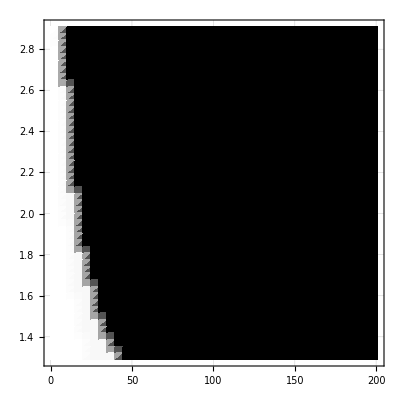

```mathematica
ListDensityPlot[UGC7321testnew5pc,DataRange->{{0,200.8},{1.29,2.91},InterpolationOrder->0},GridLines->Automatic,ColorFunction->GrayLevel]
```

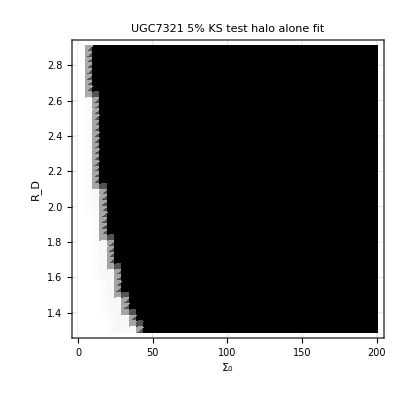

```mathematica
Show[ListDensityPlot[UGC7321testnew5pc,DataRange->{{0,200.8},{1.29,2.91},InterpolationOrder->0},GridLines->Automatic,ColorFunction->GrayLevel],FrameLabel->{{HoldForm[Subscript[R, D]],None},{HoldForm[Subscript[Σ, 0]],None}},PlotLabel->HoldForm["UGC7321 5% KS test halo alone fit"],LabelStyle->{FontFamily->"Lato",GrayLevel[0]}]
```

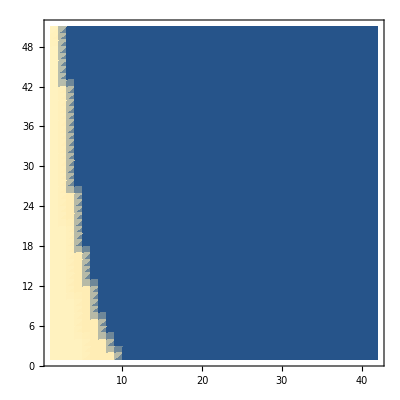

```mathematica
ListDensityPlot[UGC7321testnew5pc]
```

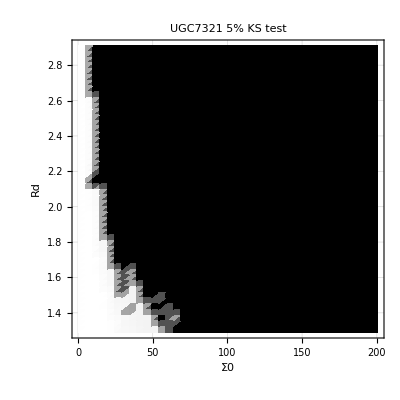
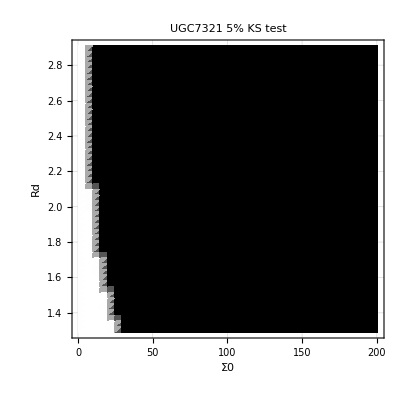
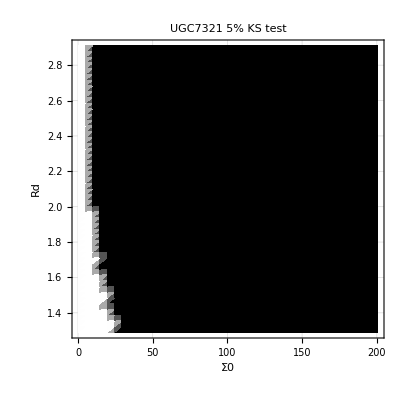

```mathematica
Table[Show[ListDensityPlot[a,DataRange->{{0,200.8},{1.29,2.91},InterpolationOrder->0},GridLines->Automatic,ColorFunction->GrayLevel],FrameLabel->{{HoldForm[Rd],None},{HoldForm[Σ0],None}},PlotLabel->HoldForm["UGC7321   5% KS test"],LabelStyle->{FontFamily->"Lato",GrayLevel[0]}],{a,{UGC7321testnew5pc,UGC7321testnew2pc,UGC7321testnew1pc}}]
```

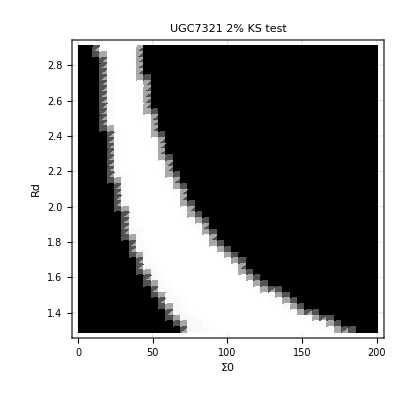
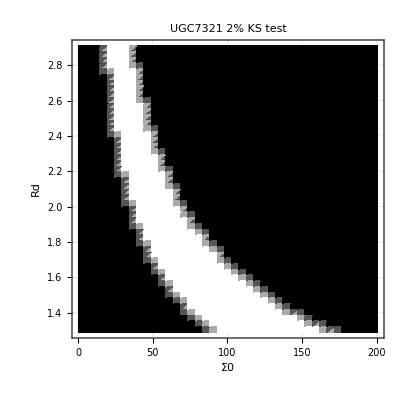
```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
UGC7321test5pc = Table[Table[PearsonChiSquareTest[RotdataUGC7321,VnettestUGC7321[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.95],{n,1,42}],{m,1,51}];
```

```mathematica
UGC7321test2pc = Table[Table[PearsonChiSquareTest[RotdataUGC7321,VnettestUGC7321[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.98],{n,1,42}],{m,1,51}];
```

```mathematica
UGC7321test1pc = Table[Table[PearsonChiSquareTest[RotdataUGC7321,VnettestUGC7321[[m]][[n]],"HypothesisTestData",SignificanceLevel->0.99],{n,1,42}],{m,1,51}];
```

```mathematica
UGC7321testconclusions5pc = Table[Table[UGC7321test5pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,51}];
```

```mathematica
UGC7321testconclusions2pc = Table[Table[UGC7321test2pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,51}];
```

```mathematica
UGC7321testconclusions1pc = Table[Table[UGC7321test1pc[[m]][[n]]["ShortTestConclusion"],{n,1,42}],{m,1,51}];
```

```mathematica
UGC7321testnew5pc = UGC7321testconclusions5pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
UGC7321testnew2pc = UGC7321testconclusions2pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
UGC7321testnew1pc = UGC7321testconclusions1pc/.{"Do not reject" -> 1,"Reject"-> 0};
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<42,n++,If[UGC7321testconclusions5pc[[m]][[n]]== "Do not reject" ,UGC7321testnew5pc[[m]][[n]] = UGC7321test5pc[[m]][[n]]["PValue"],UGC7321testnew5pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<42,n++,If[UGC7321testconclusions2pc[[m]][[n]]== "Do not reject" ,UGC7321testnew2pc[[m]][[n]] =UGC7321test2pc[[m]][[n]]["PValue"],UGC7321testnew2pc[[m]][[n]] =0]] ]
```

```mathematica
For[m=1,m<51,m++,For[n=1,n<42,n++,If[UGC7321testconclusions1pc[[m]][[n]]== "Do not reject" ,UGC7321testnew1pc[[m]][[n]] =UGC7321test1pc[[m]][[n]]["PValue"],UGC7321testnew1pc[[m]][[n]] =0]] ]
```

```mathematica
Table[MatrixPlot[a,PlotTheme->"Scientific",GridLines->Automatic,ColorFunction->GrayLevel],{a,{UGC7321testnew5pc,UGC7321testnew2pc,UGC7321testnew1pc}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
verticle
```

{1.29618,1.32858,1.36099,1.39339,1.42579,1.4582,1.4906,1.52301,1.55541,1.58782,1.62022,1.65262,1.68503,1.71743,1.74984,1.78224,1.81465,1.84705,1.87946,1.91186,1.94426,1.97667,2.00907,2.04148,2.07388,2.10629,2.13869,2.1711,2.2035,2.2359,2.26831,2.30071,2.33312,2.36552,2.39793,2.43033,2.46273,2.49514,2.52754,2.55995,2.59235,2.62476,2.65716,2.68957,2.72197,2.75437,2.78678,2.81918,2.85159,2.88399,2.9164}

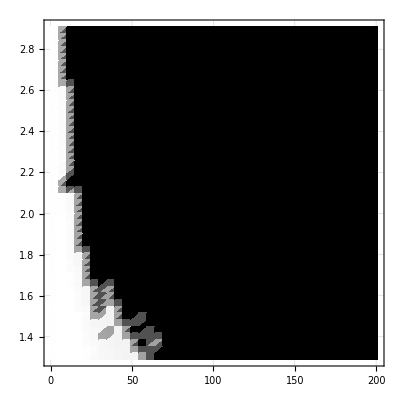

```mathematica
ListDensityPlot[UGC7321testnew5pc,DataRange->{{0,200.8},{1.29,2.91},InterpolationOrder->0},GridLines->Automatic,ColorFunction->GrayLevel]
```

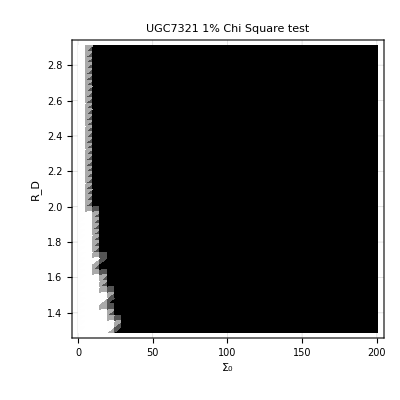

```mathematica
Show[ListDensityPlot[UGC7321testnew1pc,DataRange->{{0,200.8},{1.29,2.91},InterpolationOrder->0},GridLines->Automatic,ColorFunction->GrayLevel],FrameLabel->{{HoldForm[Subscript[R, D]],None},{HoldForm[Subscript[Σ, 0]],None}},PlotLabel->HoldForm["UGC7321 1% Chi Square test"],LabelStyle->{FontFamily->"Lato",GrayLevel[0]}]
```

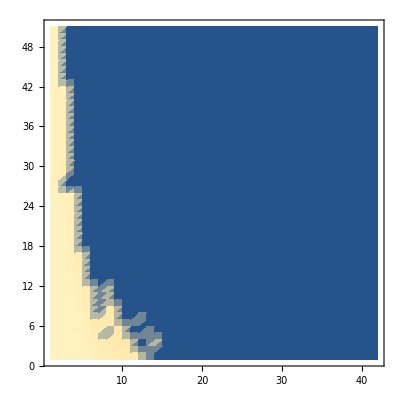

```mathematica
ListDensityPlot[UGC7321testnew5pc]
```

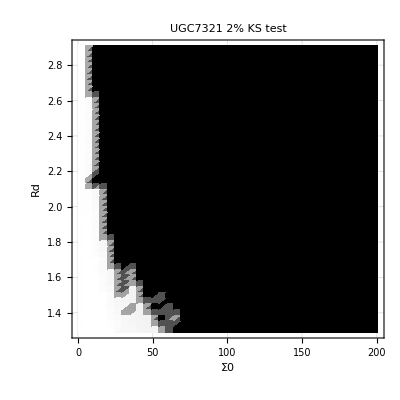
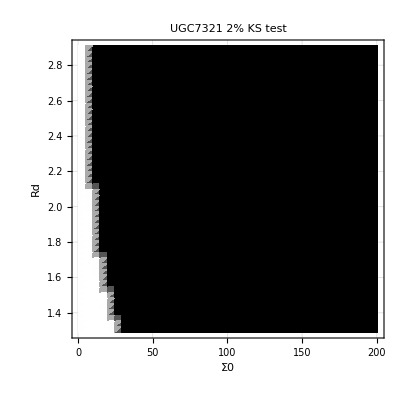
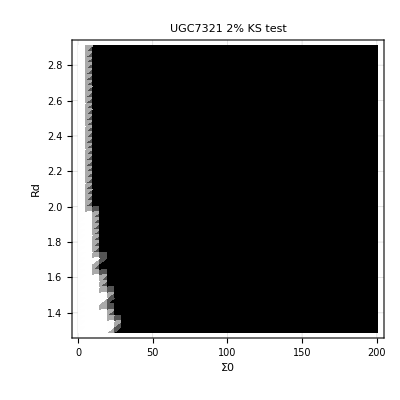

```mathematica
Table[Show[ListDensityPlot[a,DataRange->{{0,200.8},{1.29,2.91},InterpolationOrder->0},GridLines->Automatic,ColorFunction->GrayLevel],FrameLabel->{{HoldForm[Rd],None},{HoldForm[Σ0],None}},PlotLabel->HoldForm["UGC7321   2% KS test"],LabelStyle->{FontFamily->"Lato",GrayLevel[0]}],{a,{UGC7321testnew5pc,UGC7321testnew2pc,UGC7321testnew1pc}}]
```

```mathematica
okVnettest3[[1]][[1]]
```

Part::partd: Part specification okVnettest3⟦1⟧ is longer than depth of object.

okVnettest3

```mathematica
newokVnettest3 =  Table[Table[Table[{RdataUGC7321[[q]],okVnettest3[[m]][[n]][[q]]},{q,1,28}],{n,1,42}] ,{m,1,51}]
```

Part::partd: Part specification okVnettest3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of okVnettest3⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{1}
 |  |  |  |

```mathematica
Dimensions[newokVnettest3]
```

{51,42,28,2}

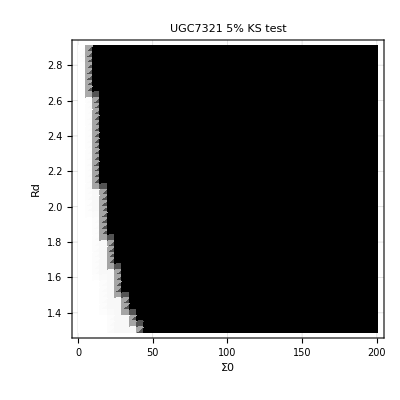
```mathematica
Export["cool.tex",-Graphics-]
```

TeXForm::unspt: TeXForm of ItemBox[PaneBox[GraphicsBox[«1»],Alignment→{Center,Baseline},BaselinePosition→Baseline],DefaultBaseStyle→Labeled] is not supported.

TeXForm::unspt: TeXForm of ItemBox[FormBox[FormBox[Null,TraditionalForm],TraditionalForm],DefaultBaseStyle→LabeledLabel] is not supported.

cool.tex

```mathematica
SystemOpen["cool.tex"]
```

```mathematica
Vnet[R]
```

√(8.3869×10^-16 R Rc^2 ρ0 (1/(R (1+R^2/Rc^2))+(1. R)/(R^2+Rc^2)-(R Rc ArcTan[(√(R^2))/Rc])/((R^2)^(3/2)))+(2.09672×10^-16 Σ0 (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)]))/Rd)

```mathematica
Export["cool.tex",Report.nb]
```

cool.tex

```mathematica
SystemOpen["cool.tex"]
```

```mathematica
SystemOpen["cool.tex"]
```

```mathematica
Vnet[R 3.086 10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd->Subscript[Rd, UGC7321],ρ0->a ρUGC7321,Rc->b RcUGC7321}/.{a->2.2048804456029933,b->0.5470606485101092}
```

√(3.92034×10^23 R ((3.24044×10^-20)/(R (1+0.534625 R^2))+(3.086×10^19 R)/(1.78132×10^39+9.5234×10^38 R^2)-(4.43179×10^-20 R ArcTan[0.73118 √(R^2)])/((R^2)^(3/2)))+3.39117×10^-37 (9.5234×10^38 R^2 BesselI[0,0.238095 R] BesselK[0,0.238095 R]-9.5234×10^38 R^2 BesselI[1,0.238095 R] BesselK[1,0.238095 R]))

```mathematica
KolmogorovSmirnovTest[RotdataUGC7321,Vnet[R 3.086 10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd->Subscript[Rd, UGC7321],ρ0->a ρUGC7321,Rc->b RcUGC7321}/.{a->2.2048804456029933,b->0.5470606485101092},"HypothesisTestData",SignificanceLevel->0.95]
```

KolmogorovSmirnovTest::rctnlndst: The argument √(3.92034×10^23 R ((3.24044×10^-20)/(R (1+0.534625 Power[«2»]))+(3.086×10^19 R)/(1.78132×10^39+9.5234×10^38 Power[«2»])-(4.43179×10^-20 R ArcTan[0.73118 √Power[«2»]])/((R^2)^(3/2)))+3.39117×10^-37 (9.5234×10^38 R^2 BesselI[0,0.238095 R] BesselK[0,0.238095 R]-9.5234×10^38 R^2 BesselI[1,0.238095 R] BesselK[1,0.238095 R])) at position 2 should be a valid distribution or a rectangular array of real numbers with length greater than the dimension of the array. The dimensionality of the arguments at positions 1 and 2 must match.

KolmogorovSmirnovTest[{{0.436332,24.85},{0.872665,39.6},{1.309,52.65},{1.74533,63.5},{2.18166,72.25},{2.61799,84.7},{3.05433,84.1},{3.49066,91.25},{3.92699,91.45},{4.36332,92.95},{4.79966,94.75},{5.23599,96.55},{5.67232,100.6},{6.10865,99.85},{6.54499,102.45},{6.98132,101.8},{7.41765,102.45},{7.85398,103.75},{8.29032,106.45},{8.72665,106.6},{9.16298,104.85},{9.59931,104.25},{10.0356,105.3},{10.472,103.25},{10.9083,103.3},{11.3446,102.95},{11.781,104.75},{12.2173,98.75}},√(3.92034×10^23 R ((3.24044×10^-20)/(R (1+0.534625 R^2))+(3.086×10^19 R)/(1.78132×10^39+9.5234×10^38 R^2)-(4.43179×10^-20 R ArcTan[0.73118 √(R^2)])/((R^2)^(3/2)))+3.39117×10^-37 (9.5234×10^38 R^2 BesselI[0,0.238095 R] BesselK[0,0.238095 R]-9.5234×10^38 R^2 BesselI[1,0.238095 R] BesselK[1,0.238095 R])),HypothesisTestData,SignificanceLevel→0.95]

```mathematica
Import["/home/yajur/Desktop/GalacticDynamics/ugc7321.dat"]
```

{{#,r(kpc),(km/sVc,â.80.93,V(0)},{-12.2173,494.7,87.9},{-11.781,508.6,101.8},{-11.3446,507.6,100.8},{-10.9083,508.2,101.4},{-10.472,506.3,99.5},{-10.0356,505.8,99},{-9.59931,504.2,97.4},{-9.16298,507.1,100.3},{-8.72665,506.6,99.8},{-8.29032,507.8,101},{-7.85398,506.5,99.7},{-7.41765,504.7,97.9},{-6.98132,505.2,98.4},{-6.54499,506.1,99.3},{-6.10865,508.3,101.5},{-5.67232,507.3,100.5},{-5.23599,504,97.2},{-4.79966,499.9,93.1},{-4.36332,497.7,90.9},{-3.92699,497.4,90.6},{-3.49066,497,90.2},{-3.05433,493.9,87.1},{-2.61799,492.6,85.8},{-2.18166,477.7,70.9},{-1.74533,468.3,61.5},{-1.309,461.1,54.3},{-0.872665,449.6,42.8},{-0.436332,433.1,26.3},{0,406.8,0},{0.436332,383.4,-23.4},{0.872665,370.4,-36.4},{1.309,355.8,-51},{1.74533,341.3,-65.5},{2.18166,333.2,-73.6},{2.61799,323.2,-83.6},{3.05433,325.7,-81.1},{3.49066,314.5,-92.3},{3.92699,314.5,-92.3},{4.36332,311.8,-95},{4.79966,310.4,-96.4},{5.23599,310.9,-95.9},{5.67232,306.1,-100.7},{6.10865,308.6,-98.2},{6.54499,301.2,-105.6},{6.98132,301.6,-105.2},{7.41765,299.8,-107},{7.85398,299,-107.8},{8.29032,294.9,-111.9},{8.72665,293.4,-113.4},{9.16298,297.4,-109.4},{9.59931,295.7,-111.1},{10.0356,295.2,-111.6},{10.472,299.8,-107},{10.9083,301.6,-105.2},{11.3446,301.7,-105.1},{11.781,299.1,-107.7},{12.2173,297.2,-109.6},{}}

```mathematica
ugc =Drop[ {{-12.2173,494.7,87.9},{-11.781,508.6,101.8},{-11.3446,507.6,100.8},{-10.9083,508.2,101.4},{-10.472,506.3,99.5},{-10.0356,505.8,99},{-9.59931,504.2,97.4},{-9.16298,507.1,100.3},{-8.72665,506.6,99.8},{-8.29032,507.8,101},{-7.85398,506.5,99.7},{-7.41765,504.7,97.9},{-6.98132,505.2,98.4},{-6.54499,506.1,99.3},{-6.10865,508.3,101.5},{-5.67232,507.3,100.5},{-5.23599,504,97.2},{-4.79966,499.9,93.1},{-4.36332,497.7,90.9},{-3.92699,497.4,90.6},{-3.49066,497,90.2},{-3.05433,493.9,87.1},{-2.61799,492.6,85.8},{-2.18166,477.7,70.9},{-1.74533,468.3,61.5},{-1.309,461.1,54.3},{-0.872665,449.6,42.8},{-0.436332,433.1,26.3},{0,406.8,0},{0.436332,383.4,-23.4},{0.872665,370.4,-36.4},{1.309,355.8,-51},{1.74533,341.3,-65.5},{2.18166,333.2,-73.6},{2.61799,323.2,-83.6},{3.05433,325.7,-81.1},{3.49066,314.5,-92.3},{3.92699,314.5,-92.3},{4.36332,311.8,-95},{4.79966,310.4,-96.4},{5.23599,310.9,-95.9},{5.67232,306.1,-100.7},{6.10865,308.6,-98.2},{6.54499,301.2,-105.6},{6.98132,301.6,-105.2},{7.41765,299.8,-107},{7.85398,299,-107.8},{8.29032,294.9,-111.9},{8.72665,293.4,-113.4},{9.16298,297.4,-109.4},{9.59931,295.7,-111.1},{10.0356,295.2,-111.6},{10.472,299.8,-107},{10.9083,301.6,-105.2},{11.3446,301.7,-105.1},{11.781,299.1,-107.7},{12.2173,297.2,-109.6}},None,{2}]
```

{{-12.2173,87.9},{-11.781,101.8},{-11.3446,100.8},{-10.9083,101.4},{-10.472,99.5},{-10.0356,99},{-9.59931,97.4},{-9.16298,100.3},{-8.72665,99.8},{-8.29032,101},{-7.85398,99.7},{-7.41765,97.9},{-6.98132,98.4},{-6.54499,99.3},{-6.10865,101.5},{-5.67232,100.5},{-5.23599,97.2},{-4.79966,93.1},{-4.36332,90.9},{-3.92699,90.6},{-3.49066,90.2},{-3.05433,87.1},{-2.61799,85.8},{-2.18166,70.9},{-1.74533,61.5},{-1.309,54.3},{-0.872665,42.8},{-0.436332,26.3},{0,0},{0.436332,-23.4},{0.872665,-36.4},{1.309,-51},{1.74533,-65.5},{2.18166,-73.6},{2.61799,-83.6},{3.05433,-81.1},{3.49066,-92.3},{3.92699,-92.3},{4.36332,-95},{4.79966,-96.4},{5.23599,-95.9},{5.67232,-100.7},{6.10865,-98.2},{6.54499,-105.6},{6.98132,-105.2},{7.41765,-107},{7.85398,-107.8},{8.29032,-111.9},{8.72665,-113.4},{9.16298,-109.4},{9.59931,-111.1},{10.0356,-111.6},{10.472,-107},{10.9083,-105.2},{11.3446,-105.1},{11.781,-107.7},{12.2173,-109.6}}

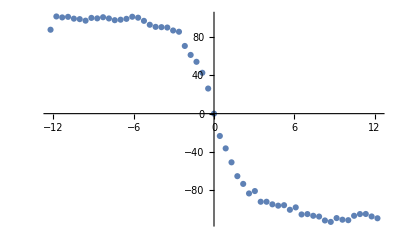

```mathematica
ListPlot[ugc]
```

```mathematica
Show[ListPlot[RotdataUGC7321,PlotStyle->Black],Plot[{Vnet[R 3.086 10^19]/.{Σ0->Subscript[Σ, UGC7321],Rd->Subscript[Rd, UGC7321],ρ0->a ρUGC7321,Rc->b RcUGC7321}}/.{a->2.2048804456029933,b->0.5470606485101092},{R,0.436332,12.2173}],FrameLabel->{HoldForm["R (kpc)"],HoldForm["Rotation Velocity " "(km s^-1)"]},LabelStyle->Directive[Black,FontSize->12],PlotLabel->HoldForm[UGC7321],LabelStyle->{GrayLevel[0]},Frame->True]
```

-Graphics-

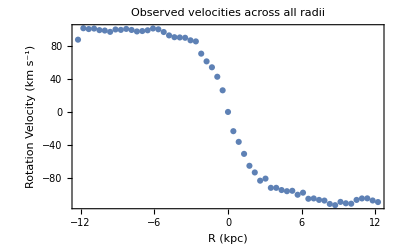

```mathematica
Show[ListPlot[ugc],Frame->True,FrameLabel->{HoldForm["R (kpc)"],HoldForm["Rotation Velocity " "(km s^-1)"]},PlotLabel->HoldForm[Observed velocities across all radii],LabelStyle->{GrayLevel[0]},LabelStyle->Directive[Black,FontSize->12]]
```

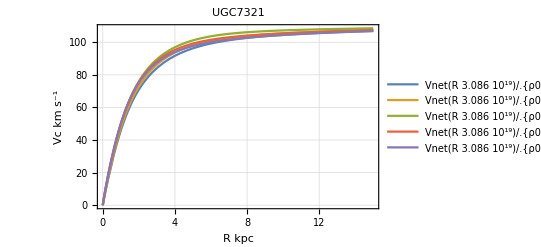

```mathematica
Plot[{Vnet[R*3.086*10^19]/.{ρ0->a*ρUGC7321,Rc->b*RcUGC7321,Σ0->Subscript[Σ, UGC7321],Rd-> Subscript[Rd, UGC7321]}/.{a->2.2048804456029933,b->0.5470606485101092},Vnet[R*3.086*10^19]/.{ρ0->a*ρUGC7321,Rc->b*RcUGC7321,Σ0->(70/50.2)*Subscript[Σ, UGC7321],Rd->(2/2.1)* Subscript[Rd, UGC7321]}/.{a->2.2048804456029933,b->0.5470606485101092},Vnet[R*3.086*10^19]/.{ρ0->a*ρUGC7321,Rc->b*RcUGC7321,Σ0->(100/50.2)*Subscript[Σ, UGC7321],Rd->(2/2.1)* Subscript[Rd, UGC7321]}/.{a->2.2048804456029933,b->0.5470606485101092},Vnet[R*3.086*10^19]/.{ρ0->a*ρUGC7321,Rc->b*RcUGC7321,Σ0->(100/50.2)*Subscript[Σ, UGC7321],Rd->(1.7/2.1)* Subscript[Rd, UGC7321]}/.{a->2.2048804456029933,b->0.5470606485101092},Vnet[R*3.086*10^19]/.{ρ0->a*ρUGC7321,Rc->b*RcUGC7321,Σ0->(100/50.2)*Subscript[Σ, UGC7321],Rd->(1.5/2.1)* Subscript[Rd, UGC7321]}/.{a->2.2048804456029933,b->0.5470606485101092}},{R,0,15},Frame->True,FrameLabel->{HoldForm[R kpc],HoldForm["Vc km s^-1"]},PlotLabel->HoldForm[UGC7321 ],LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions",GridLines->Automatic,PlotRange->All]
```